```mathematica
ClearAll["Global`*"]
```

## Beginning stuff

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

Initialize J-V, J_E-V data

```mathematica
orbit=1694;
```

```mathematica
makePlots=1;
```

#### pot offset (in V)?

```mathematica
potTFactor=0;
```

```mathematica
If[potTFactor == 0,potFactorString="",potFactorString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

#### Spectra average interval?

```mathematica
spectraAverageInterval=2;
```

```mathematica
specAvgItvlString=If[spectraAverageInterval==2,"",ToString@StringForm["-avgItvl`1`",spectraAverageInterval]];
```

### And the data ...

```mathematica
peakEBoundsIndShift=0;
```

```mathematica
peakEBoundsIndShift=False;
```

#### peakEBounds shift selection and string setup

```mathematica
peakEBoundsSuff="";If[ToString[Head[peakEBoundsIndShift]]=="Integer",peakEBoundsSuff=ToString@StringForm["-peakE_indShift_eq_`1`",peakEBoundsIndShift]];
```

#### These use peakE_bounds_indShift=[-1,0] (initialize these)

```mathematica
time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,407.68,815.36,344.96,1128.96,344.96,344.96,344.96,344.96,344.96,564.48,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,344.96,407.68,344.96,344.96,407.68,344.96,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,815.36,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,407.68,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,678.72,665.28,788.48,616.00,1232.00,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,344.96,407.68,564.48,564.48,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.00,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3360.00,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,344.96,344.96,1128.96,1128.96,940.80,1128.96,407.68,344.96,344.96,1379.84,815.36,940.80,815.36,940.80,940.80,940.80,689.92,344.96,344.96,344.96,344.96,344.96,344.96,1379.84,344.96,344.96,407.68,470.40,344.96,344.96};
curs={0.443,0.381,0.400,0.356,0.353,0.288,0.217,0.373,0.314,0.337,0.402,0.308,0.201,0.199,0.133,0.233,0.166,0.169,0.178,0.596,0.229,0.438,0.670,1.405,1.407,0.395,0.104,0.131,0.500,1.145,1.473,1.614,1.489,2.619,2.488,1.543,1.007,0.997,1.111,1.318,1.430,2.460,1.954,1.357,0.835,0.624,0.247,0.162,0.165,0.176,0.145,0.171,0.190,0.266,0.420,0.755,0.849,0.929,1.045,1.055,0.960,0.900,0.814,1.004,1.005,0.952,0.961,1.126,1.045,1.261,0.777,0.884,0.649,0.412,0.558,0.617,0.837,0.786,0.733,0.701,0.788,0.873,0.777,0.678,0.537,0.522,0.405,0.396,0.404,0.393,0.519,0.526,0.463,0.457,0.518,0.608,0.613,0.595,0.655,0.648,0.713,0.857,0.798,1.129,1.224,1.417,1.425,1.261,1.388,1.427,1.443,1.683,1.575,1.519,1.170,1.186,0.914,1.148,1.110,1.213,1.315,1.585,1.913,2.163,2.486,2.430,2.591,2.637,2.387,2.262,2.344,2.030,2.064,2.194,3.582,4.924,5.407,5.627,5.219,4.690,4.253,3.906,3.509,2.756,2.830,2.388,2.350,1.958,0.755,0.462,0.098,0.048,0.077,0.278,0.949,1.341,1.776,2.314,2.185,1.431,1.193,0.677,0.656,0.800,0.898,0.828,0.859,0.940,1.042,0.888,0.923,0.798,1.094,0.844,1.187,0.941,0.753,0.818,0.964,0.740,0.788,0.859,0.874,0.787,0.828,0.858,0.919,0.929,0.964,0.996,1.030,1.315,1.283,1.360,1.380,1.416,1.326,1.451,1.682,1.852,1.966,1.823,1.869,1.767,1.553,1.586,1.545,1.670,1.586,1.542,1.497,1.870,1.904,1.913,1.869,1.878,1.681,1.425,1.371,2.006,3.038,3.490,3.041,2.593,2.938,2.536,4.619,2.203,0.715,0.569,0.792,0.709,0.730,1.140,1.400,1.168,0.508,0.586,0.673,0.706,0.914,1.384,0.797,0.940,1.163,0.974,0.731,1.303,1.213,1.223,1.022,1.047,1.228,1.982,1.810,1.597,1.336};
curErrs={0.026,0.035,0.029,0.039,0.027,0.031,0.025,0.030,0.022,0.030,0.029,0.032,0.017,0.029,0.034,0.066,0.027,0.050,0.032,0.036,0.018,0.037,0.037,0.059,0.052,0.063,0.030,0.014,0.026,0.040,0.043,0.051,0.044,0.065,0.071,0.056,0.045,0.038,0.037,0.053,0.046,0.068,0.062,0.055,0.044,0.030,0.028,0.019,0.025,0.027,0.022,0.020,0.029,0.029,0.027,0.032,0.035,0.044,0.040,0.044,0.047,0.039,0.044,0.050,0.046,0.053,0.046,0.059,0.070,0.068,0.042,0.053,0.063,0.042,0.041,0.034,0.051,0.041,0.034,0.037,0.045,0.047,0.043,0.065,0.047,0.037,0.038,0.048,0.043,0.062,0.040,0.051,0.054,0.044,0.043,0.045,0.074,0.051,0.059,0.026,0.027,0.026,0.026,0.029,0.031,0.038,0.034,0.033,0.038,0.038,0.037,0.041,0.043,0.041,0.033,0.035,0.033,0.035,0.033,0.035,0.039,0.046,0.048,0.046,0.060,0.054,0.053,0.057,0.056,0.056,0.056,0.060,0.064,0.071,0.084,0.116,0.122,0.137,0.124,0.129,0.099,0.089,0.086,0.072,0.070,0.067,0.066,0.061,0.037,0.029,0.011,0.010,0.014,0.032,0.042,0.052,0.066,0.080,0.075,0.052,0.056,0.045,0.038,0.037,0.051,0.044,0.041,0.047,0.047,0.046,0.070,0.049,0.079,0.055,0.054,0.061,0.057,0.048,0.051,0.051,0.066,0.051,0.048,0.045,0.049,0.054,0.058,0.062,0.059,0.059,0.053,0.077,0.079,0.087,0.082,0.090,0.112,0.103,0.101,0.108,0.114,0.117,0.114,0.127,0.179,0.134,0.093,0.098,0.109,0.112,0.129,0.160,0.144,0.153,0.116,0.076,0.084,0.127,0.080,0.061,0.040,0.059,0.056,0.054,0.040,0.050,0.068,0.054,0.036,0.035,0.043,0.040,0.046,0.050,0.058,0.076,0.087,0.150,0.083,0.107,0.085,0.089,0.150,0.056,0.043,0.055,0.037,0.052,0.047,0.048,0.058,0.068,0.046,0.075,0.060,0.072,0.059};
jes={0.298,0.246,0.258,0.262,0.240,0.193,0.142,0.246,0.183,0.204,0.204,0.173,0.146,0.147,0.132,0.191,0.140,0.164,0.157,0.312,0.174,0.262,0.369,0.660,0.761,0.231,0.106,0.141,0.324,0.727,0.975,1.177,1.194,2.619,2.779,1.707,0.973,0.943,1.157,1.413,1.564,3.246,2.605,1.481,0.872,0.556,0.256,0.203,0.202,0.198,0.178,0.198,0.248,0.297,0.412,0.673,0.797,0.887,1.034,1.057,0.994,0.974,0.894,1.137,1.045,1.039,1.045,1.459,1.322,1.407,0.620,0.586,0.480,0.301,0.397,0.438,0.608,0.543,0.512,0.505,0.544,0.579,0.525,0.466,0.415,0.388,0.289,0.283,0.281,0.261,0.356,0.366,0.326,0.336,0.385,0.431,0.440,0.439,0.505,0.516,0.608,0.784,0.723,1.175,1.281,1.464,1.572,1.409,1.506,1.504,1.572,1.962,1.735,1.812,1.956,2.082,1.592,2.192,2.186,2.548,2.952,3.999,5.441,6.827,8.725,9.140,10.112,10.042,9.136,8.720,8.653,7.230,7.551,8.009,13.617,19.492,19.109,18.375,14.677,11.324,8.566,6.235,5.396,3.428,2.804,2.233,2.027,1.447,0.435,0.276,0.085,0.042,0.063,0.190,0.769,1.780,3.038,4.677,4.450,2.308,1.693,0.794,0.743,0.976,1.170,1.117,1.200,1.346,1.633,1.341,1.549,1.291,1.948,1.412,2.309,1.636,0.997,1.048,1.257,0.945,1.090,1.131,1.211,1.204,1.240,1.308,1.431,1.390,1.347,1.431,1.746,2.561,2.470,2.665,2.697,2.892,2.763,3.070,3.426,4.073,4.321,3.852,3.694,3.536,3.158,3.329,3.146,3.506,3.126,2.902,2.932,3.983,4.038,4.421,4.468,3.397,2.844,2.298,2.192,2.624,2.943,2.960,2.520,2.128,2.151,2.046,3.792,1.854,0.802,0.704,0.986,0.837,0.942,1.223,1.209,0.962,0.646,0.718,0.798,0.825,1.046,1.413,0.915,0.973,0.997,0.837,0.703,1.190,1.270,1.132,1.155,0.997,1.045,1.323,1.291,1.163,1.107};
jeErrs={0.071,0.099,0.079,0.104,0.067,0.159,0.078,0.091,0.068,0.139,0.082,0.068,0.134,0.123,0.188,0.136,0.091,0.090,0.060,0.118,0.119,0.107,0.110,0.173,0.748,0.128,0.085,0.077,0.155,0.109,0.126,0.144,0.156,0.214,0.259,0.205,0.150,0.129,0.120,0.180,0.162,0.268,0.247,0.200,0.174,0.123,0.095,0.085,0.084,0.105,0.119,0.084,0.130,0.127,0.080,0.095,0.131,0.147,0.148,0.157,0.155,0.168,0.199,0.167,0.188,0.181,0.150,0.217,0.392,0.255,0.140,0.133,0.152,0.091,0.126,0.119,0.138,0.113,0.099,0.157,0.123,0.139,0.116,0.152,0.149,0.141,0.102,0.123,0.092,0.115,0.114,0.122,0.132,0.103,0.106,0.149,1.104,0.148,0.173,0.170,0.148,0.112,0.102,0.146,0.155,0.176,0.155,0.151,0.218,0.162,0.174,0.189,0.168,0.164,0.145,0.159,0.153,0.174,0.155,0.185,0.216,0.264,0.291,0.289,0.426,0.387,0.367,0.407,0.420,0.407,0.385,0.408,0.405,0.460,0.559,0.788,0.710,0.776,0.586,0.515,0.344,0.303,0.293,0.206,0.209,0.192,0.186,0.172,0.125,0.090,0.030,0.024,0.125,0.071,0.112,0.189,0.338,0.409,0.376,0.239,0.249,0.168,0.156,0.187,0.308,0.247,0.204,0.255,0.253,0.241,0.398,0.300,2.108,0.342,0.305,0.309,0.274,0.216,0.202,0.207,0.341,0.236,0.193,0.215,0.236,0.244,0.324,0.336,0.300,0.301,0.285,0.556,0.500,0.545,0.495,0.617,0.723,0.655,0.643,0.682,0.748,0.687,0.702,0.786,1.026,0.736,0.506,0.589,0.636,0.582,0.662,0.879,0.824,0.948,0.585,0.386,0.713,0.452,0.304,0.176,0.180,0.201,0.159,0.182,0.193,0.161,0.221,0.167,0.112,0.106,0.136,0.127,0.152,0.138,0.132,0.176,0.229,0.816,0.218,0.635,0.510,0.279,0.402,0.146,0.125,0.119,0.150,0.134,0.155,0.184,0.166,0.156,0.122,0.184,0.175,0.172,0.174};
dataset=1;
```

#### These are derived using peakE_bounds_indShift=[0,0]

```mathematica
If[peakEBoundsIndShift==0,time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,282.24,235.20,235.20,203.84,344.96,235.20,344.96,282.24,235.20,203.84,203.84,203.84,203.84,203.84,235.20,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.20,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,203.84,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,203.84,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,678.72,665.28,725.76,553.28,1232.00,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,203.84,407.68,282.24,203.84,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.00,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3360.00,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.20,203.84,1128.96,203.84,203.84,235.20,1379.84,815.36,940.80,815.36,203.84,203.84,940.80,282.24,235.20,235.20,203.84,344.96,282.24,235.20,1379.84,344.96,344.96,407.68,470.40,344.96,282.24};
curs={0.324,0.251,0.326,0.108,0.353,0.322,0.248,0.463,0.246,0.391,0.288,0.308,0.240,0.293,0.168,0.296,0.212,0.215,0.198,0.596,0.229,0.619,0.670,1.040,1.671,0.559,0.124,0.142,0.500,0.789,1.159,0.752,0.905,1.166,1.529,0.770,0.614,0.597,0.575,0.729,0.873,1.232,1.069,0.878,0.542,0.712,0.122,0.102,0.135,0.094,0.096,0.083,0.094,0.117,0.470,0.578,0.666,0.615,0.732,0.735,0.690,0.677,0.622,0.715,0.839,0.728,0.777,0.821,0.666,0.840,0.606,0.699,0.572,0.412,0.558,0.521,0.554,0.576,0.632,0.489,0.660,0.648,0.648,0.587,0.404,0.392,0.334,0.321,0.338,0.325,0.391,0.431,0.348,0.426,0.460,0.562,0.477,0.471,0.595,0.535,0.449,0.740,0.668,0.917,0.727,0.841,0.763,0.913,0.921,0.912,0.963,0.988,1.071,0.987,0.767,0.586,0.621,0.753,0.770,0.718,0.907,0.967,0.966,0.932,1.508,1.293,1.519,1.485,1.330,1.263,1.093,1.253,0.948,0.998,1.694,1.619,1.342,2.081,1.290,1.577,1.373,1.209,1.354,0.874,1.352,0.950,1.064,0.793,0.591,0.627,0.077,0.048,0.093,0.176,0.457,0.757,0.888,1.265,1.146,0.902,0.802,0.396,0.447,0.666,0.686,0.680,0.764,0.543,0.826,0.599,0.771,0.622,0.751,0.703,0.746,0.590,0.369,0.560,0.729,0.481,0.608,0.587,0.657,0.514,0.502,0.580,0.626,0.601,0.832,0.561,0.583,0.794,0.764,0.854,0.867,0.706,0.673,0.808,0.858,1.144,1.232,1.067,1.293,1.228,0.797,0.935,0.781,0.936,1.049,0.913,0.918,1.106,1.145,0.743,0.917,0.879,0.862,0.609,0.568,1.820,2.311,2.225,2.290,2.126,2.031,2.144,2.971,2.203,0.969,0.643,0.850,0.800,0.377,1.370,1.921,1.313,0.188,0.361,0.357,0.434,1.077,1.708,0.403,0.940,1.303,1.127,0.916,1.118,1.213,1.356,0.332,0.927,1.048,1.283,1.092,1.291,1.336};
curErrs={0.025,0.026,0.023,0.020,0.027,0.028,0.025,0.034,0.017,0.031,0.023,0.032,0.018,0.029,0.031,0.057,0.032,0.057,0.029,0.036,0.018,0.036,0.037,0.051,0.040,0.049,0.042,0.015,0.026,0.033,0.040,0.038,0.041,0.050,0.057,0.043,0.034,0.033,0.032,0.039,0.039,0.049,0.043,0.043,0.031,0.026,0.013,0.013,0.025,0.019,0.013,0.013,0.016,0.019,0.026,0.032,0.033,0.036,0.033,0.038,0.037,0.035,0.038,0.043,0.043,0.045,0.039,0.044,0.043,0.054,0.039,0.047,0.066,0.042,0.041,0.033,0.037,0.036,0.033,0.040,0.042,0.043,0.036,0.059,0.043,0.043,0.038,0.042,0.046,0.061,0.034,0.049,0.038,0.049,0.046,0.042,0.186,0.046,0.060,0.024,0.018,0.024,0.023,0.026,0.025,0.030,0.026,0.029,0.027,0.029,0.030,0.033,0.036,0.035,0.025,0.022,0.023,0.026,0.025,0.029,0.031,0.033,0.029,0.023,0.037,0.036,0.033,0.038,0.037,0.038,0.034,0.038,0.031,0.039,0.049,0.063,0.054,0.102,0.070,0.066,0.047,0.051,0.056,0.035,0.054,0.043,0.039,0.031,0.032,0.029,0.011,0.010,0.020,0.031,0.035,0.036,0.032,0.057,0.052,0.040,0.050,0.029,0.036,0.034,0.042,0.040,0.040,0.040,0.045,0.038,0.058,0.042,0.041,0.041,0.045,0.048,0.049,0.048,0.059,0.039,0.052,0.053,0.050,0.036,0.049,0.047,0.061,0.048,0.053,0.053,0.049,0.063,0.074,0.063,0.062,0.053,0.084,0.070,0.077,0.085,0.115,0.087,0.081,0.092,0.085,0.100,0.080,0.073,0.091,0.080,0.089,0.115,0.115,0.121,0.077,0.106,0.147,0.109,0.088,0.058,0.039,0.055,0.050,0.050,0.037,0.046,0.058,0.054,0.028,0.037,0.043,0.047,0.030,0.047,0.051,0.065,0.057,0.180,0.052,0.077,0.054,0.061,0.096,0.056,0.042,0.050,0.039,0.048,0.047,0.046,0.028,0.059,0.044,0.058,0.050,0.063,0.059};
jes={0.262,0.206,0.237,0.142,0.240,0.201,0.149,0.265,0.164,0.217,0.173,0.173,0.155,0.167,0.140,0.205,0.151,0.174,0.162,0.312,0.174,0.301,0.369,0.560,0.817,0.266,0.110,0.143,0.324,0.616,0.877,0.779,0.916,1.612,2.098,1.173,0.799,0.766,0.859,1.052,1.238,2.171,1.804,1.172,0.712,0.574,0.197,0.178,0.192,0.159,0.158,0.151,0.197,0.218,0.423,0.611,0.726,0.739,0.887,0.905,0.868,0.872,0.808,0.984,0.981,0.934,0.962,1.271,1.047,1.129,0.547,0.525,0.458,0.301,0.397,0.411,0.507,0.475,0.478,0.425,0.502,0.495,0.483,0.436,0.365,0.339,0.269,0.262,0.262,0.242,0.314,0.335,0.289,0.327,0.366,0.415,0.388,0.391,0.482,0.468,0.468,0.724,0.656,1.049,0.932,1.061,1.055,1.165,1.184,1.147,1.250,1.430,1.407,1.423,1.578,1.347,1.318,1.737,1.806,1.869,2.451,3.027,3.554,3.945,6.640,6.322,7.533,7.227,6.469,6.159,5.235,5.564,4.612,5.044,9.081,10.325,8.372,11.067,6.299,6.159,4.444,3.026,3.043,1.662,1.798,1.265,1.240,0.822,0.389,0.312,0.078,0.042,0.066,0.155,0.510,1.286,1.963,3.260,3.016,1.761,1.364,0.582,0.597,0.879,0.990,0.995,1.123,0.929,1.416,1.042,1.402,1.132,1.546,1.286,1.707,1.233,0.653,0.868,1.084,0.748,0.967,0.926,1.051,0.943,0.924,1.043,1.141,1.057,1.239,0.980,1.213,1.849,1.762,1.974,2.001,1.814,1.768,2.121,2.225,3.050,3.264,2.743,2.965,2.837,2.044,2.387,2.008,2.412,2.427,2.077,2.210,2.896,2.988,2.305,2.916,2.301,2.037,1.427,1.337,2.572,2.692,2.486,2.290,1.997,1.872,1.939,3.176,1.854,0.856,0.719,0.999,0.856,0.724,1.272,1.321,0.996,0.424,0.607,0.624,0.694,1.081,1.483,0.698,0.973,1.030,0.873,0.743,1.138,1.270,1.163,0.696,0.964,0.995,1.108,1.047,1.077,1.107};
jeErrs={0.140,0.117,0.072,0.611,0.067,0.092,0.058,0.064,0.062,0.114,0.077,0.068,0.145,0.101,0.113,0.128,0.092,0.076,0.054,0.118,0.119,0.103,0.110,0.198,0.273,0.111,0.101,0.073,0.155,0.116,0.138,0.174,0.193,0.285,0.330,0.312,0.205,0.170,0.206,0.232,0.236,0.367,0.313,0.249,0.210,0.102,0.116,0.123,0.102,0.135,0.192,0.128,0.203,0.348,0.071,0.115,0.150,0.193,0.173,0.187,0.183,0.202,0.362,0.228,0.242,0.230,0.184,0.277,0.303,0.316,0.145,0.138,0.173,0.091,0.126,0.127,0.142,0.123,0.104,0.210,0.131,0.146,0.113,0.153,0.160,0.160,0.116,0.128,0.113,0.210,0.115,0.133,0.119,0.118,0.132,0.150,0.797,0.153,0.187,0.179,0.131,0.119,0.111,0.168,0.173,0.220,0.181,0.186,0.224,0.183,0.229,0.240,0.207,0.215,0.243,0.273,0.290,0.286,0.262,0.305,0.361,0.416,0.460,0.467,0.702,0.696,0.683,0.742,0.749,0.745,0.650,0.722,0.622,0.754,0.995,1.499,1.230,1.863,1.207,1.125,0.706,0.479,0.494,0.282,0.278,0.238,0.218,0.164,0.124,0.082,0.036,0.024,0.093,0.143,0.180,0.251,0.337,0.575,0.545,0.328,1.196,0.179,0.224,0.208,0.265,0.250,0.232,0.281,0.306,0.299,0.422,0.510,0.438,0.322,0.434,0.375,0.474,1.804,0.332,0.269,0.443,0.432,0.353,0.280,0.358,0.319,0.555,0.354,0.329,0.383,0.442,0.770,0.768,0.635,0.581,0.587,0.842,0.689,0.783,0.866,1.315,3.415,0.764,0.901,1.048,0.915,0.797,0.764,0.823,0.789,0.862,1.193,2.008,1.398,0.970,1.137,1.371,1.014,0.823,0.196,0.201,0.245,0.176,0.184,0.192,0.165,0.260,0.167,0.101,0.094,0.122,0.116,0.228,0.119,0.124,0.166,1.460,1.860,0.292,5.158,0.356,0.260,0.832,0.146,0.121,0.112,0.132,0.142,0.155,0.170,0.281,0.162,0.133,0.191,0.193,0.176,0.174};]
```

If[False==0,time={02:01:16.078,02:01:16.709,02:01:17.340,02:01:17.971,02:01:18.603,02:01:19.234,02:01:19.865,02:01:20.496,02:01:21.127,02:01:21.758,02:01:22.389,02:01:23.020,02:01:23.651,02:01:24.282,02:01:24.914,02:01:25.545,02:01:26.176,02:01:26.807,02:01:27.438,02:01:28.069,02:01:28.700,02:01:29.331,02:01:29.962,02:01:30.593,02:01:31.225,02:01:31.856,02:01:32.487,02:01:33.118,02:01:33.749,02:01:34.380,02:01:35.011,02:01:35.642,02:01:36.273,02:01:36.904,02:01:37.536,02:01:38.167,02:01:38.798,02:01:39.429,02:01:40.060,02:01:40.691,02:01:41.322,02:01:41.953,02:01:42.585,02:01:43.216,02:01:43.847,02:01:44.478,02:01:45.109,02:01:45.740,02:01:46.371,02:01:47.002,02:01:47.634,02:01:48.265,02:01:48.896,02:01:49.527,02:01:50.158,02:01:50.789,02:01:51.420,02:01:52.051,02:01:52.682,02:01:53.314,02:01:53.945,02:01:54.576,02:01:55.207,02:01:55.838,02:01:56.469,02:01:57.100,02:01:57.732,02:01:58.363,02:01:58.994,02:01:59.625,02:02:00.256,02:02:00.887,02:02:01.518,02:02:02.150,02:02:02.781,02:02:03.412,02:02:04.043,02:02:04.674,02:02:05.305,02:02:05.937,02:02:06.568,02:02:07.199,02:02:07.830,02:02:08.461,02:02:09.092,02:02:09.723,02:02:10.355,02:02:10.986,02:02:11.617,02:02:12.248,02:02:12.879,02:02:13.510,02:02:14.141,02:02:14.773,02:02:15.404,02:02:16.035,02:02:16.666,02:02:17.297,02:02:17.928,02:02:18.560,02:02:19.191,02:02:19.822,02:02:20.453,02:02:21.084,02:02:21.715,02:02:22.347,02:02:22.978,02:02:23.609,02:02:24.240,02:02:24.871,02:02:25.502,02:02:26.134,02:02:26.765,02:02:27.396,02:02:28.027,02:02:28.658,02:02:29.289,02:02:29.921,02:02:30.552,02:02:31.183,02:02:31.814,02:02:32.445,02:02:33.077,02:02:33.708,02:02:34.339,02:02:34.970,02:02:35.601,02:02:36.233,02:02:36.864,02:02:37.495,02:02:38.126,02:02:38.757,02:02:39.388,02:02:40.020,02:02:40.651,02:02:41.282,02:02:41.913,02:02:42.544,02:02:43.176,02:02:43.807,02:02:44.438,02:02:45.069,02:02:45.700,02:02:46.332,02:02:46.963,02:02:47.594,02:02:48.225,02:02:48.856,02:02:49.488,02:02:50.119,02:02:50.750,02:02:51.381,02:02:52.012,02:02:52.644,02:02:53.275,02:02:53.906,02:02:54.537,02:02:55.168,02:02:55.800,02:02:56.431,02:02:57.062,02:02:57.693,02:02:58.325,02:02:58.956,02:02:59.587,02:03:00.218,02:03:00.849,02:03:01.481,02:03:02.112,02:03:02.743,02:03:03.374,02:03:04.005,02:03:04.637,02:03:05.268,02:03:05.899,02:03:06.530,02:03:07.162,02:03:07.793,02:03:08.424,02:03:09.055,02:03:09.687,02:03:10.318,02:03:10.949,02:03:11.580,02:03:12.211,02:03:12.843,02:03:13.474,02:03:14.105,02:03:14.736,02:03:15.368,02:03:15.999,02:03:16.630,02:03:17.261,02:03:17.893,02:03:18.524,02:03:19.155,02:03:19.786,02:03:20.418,02:03:21.049,02:03:21.680,02:03:22.311,02:03:22.943,02:03:23.574,02:03:24.205,02:03:24.836,02:03:25.468,02:03:26.099,02:03:26.730,02:03:27.361,02:03:27.993,02:03:28.624,02:03:29.255,02:03:29.886,02:03:30.518,02:03:31.149,02:03:31.780,02:03:32.411,02:03:33.043,02:03:33.674,02:03:34.305,02:03:34.936,02:03:35.568,02:03:36.199,02:03:36.830,02:03:37.461,02:03:38.093,02:03:38.724,02:03:39.355,02:03:39.986,02:03:40.618,02:03:41.249,02:03:41.880,02:03:42.512,02:03:43.143,02:03:43.774,02:03:44.405,02:03:45.037,02:03:45.668,02:03:46.299,02:03:46.930,02:03:47.562,02:03:48.193,02:03:48.824,02:03:49.456,02:03:50.087,02:03:50.718,02:03:51.349,02:03:51.981,02:03:52.612,02:03:53.243,02:03:53.875,02:03:54.506,02:03:55.137,02:03:55.768,02:03:56.400,02:03:57.031,02:03:57.662};pots={407.68,407.68,344.96,940.8,282.24,235.2,235.2,203.84,344.96,235.2,344.96,282.24,235.2,203.84,203.84,203.84,203.84,203.84,235.2,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.2,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.8,940.8,940.8,1379.84,1379.84,940.8,815.36,203.84,815.36,689.92,470.4,815.36,689.92,940.8,940.8,940.8,203.84,470.4,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.8,1128.96,940.8,884.8,678.72,665.28,725.76,553.28,1232.,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.6,1630.72,1881.6,1630.72,1881.6,1881.6,2257.92,2257.92,2759.68,3261.44,3763.2,3763.2,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.2,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.6,1630.72,1128.96,1128.96,940.8,815.36,344.96,203.84,407.68,282.24,203.84,470.4,815.36,1379.84,1881.6,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.,2661.12,3162.88,2912.,2119.04,1769.6,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.,4032.,4032.,3736.32,3539.2,3539.2,3539.2,3162.88,3360.,3736.32,3539.2,3539.2,3736.32,3360.,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.,2325.12,1881.6,1881.6,344.96,470.4,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.2,203.84,1128.96,203.84,203.84,235.2,1379.84,815.36,940.8,815.36,203.84,203.84,940.8,282.24,235.2,235.2,203.84,344.96,282.24,235.2,1379.84,344.96,344.96,407.68,470.4,344.96,282.24};curs={0.324,0.251,0.326,0.108,0.353,0.322,0.248,0.463,0.246,0.391,0.288,0.308,0.24,0.293,0.168,0.296,0.212,0.215,0.198,0.596,0.229,0.619,0.67,1.04,1.671,0.559,0.124,0.142,0.5,0.789,1.159,0.752,0.905,1.166,1.529,0.77,0.614,0.597,0.575,0.729,0.873,1.232,1.069,0.878,0.542,0.712,0.122,0.102,0.135,0.094,0.096,0.083,0.094,0.117,0.47,0.578,0.666,0.615,0.732,0.735,0.69,0.677,0.622,0.715,0.839,0.728,0.777,0.821,0.666,0.84,0.606,0.699,0.572,0.412,0.558,0.521,0.554,0.576,0.632,0.489,0.66,0.648,0.648,0.587,0.404,0.392,0.334,0.321,0.338,0.325,0.391,0.431,0.348,0.426,0.46,0.562,0.477,0.471,0.595,0.535,0.449,0.74,0.668,0.917,0.727,0.841,0.763,0.913,0.921,0.912,0.963,0.988,1.071,0.987,0.767,0.586,0.621,0.753,0.77,0.718,0.907,0.967,0.966,0.932,1.508,1.293,1.519,1.485,1.33,1.263,1.093,1.253,0.948,0.998,1.694,1.619,1.342,2.081,1.29,1.577,1.373,1.209,1.354,0.874,1.352,0.95,1.064,0.793,0.591,0.627,0.077,0.048,0.093,0.176,0.457,0.757,0.888,1.265,1.146,0.902,0.802,0.396,0.447,0.666,0.686,0.68,0.764,0.543,0.826,0.599,0.771,0.622,0.751,0.703,0.746,0.59,0.369,0.56,0.729,0.481,0.608,0.587,0.657,0.514,0.502,0.58,0.626,0.601,0.832,0.561,0.583,0.794,0.764,0.854,0.867,0.706,0.673,0.808,0.858,1.144,1.232,1.067,1.293,1.228,0.797,0.935,0.781,0.936,1.049,0.913,0.918,1.106,1.145,0.743,0.917,0.879,0.862,0.609,0.568,1.82,2.311,2.225,2.29,2.126,2.031,2.144,2.971,2.203,0.969,0.643,0.85,0.8,0.377,1.37,1.921,1.313,0.188,0.361,0.357,0.434,1.077,1.708,0.403,0.94,1.303,1.127,0.916,1.118,1.213,1.356,0.332,0.927,1.048,1.283,1.092,1.291,1.336};curErrs={0.025,0.026,0.023,0.02,0.027,0.028,0.025,0.034,0.017,0.031,0.023,0.032,0.018,0.029,0.031,0.057,0.032,0.057,0.029,0.036,0.018,0.036,0.037,0.051,0.04,0.049,0.042,0.015,0.026,0.033,0.04,0.038,0.041,0.05,0.057,0.043,0.034,0.033,0.032,0.039,0.039,0.049,0.043,0.043,0.031,0.026,0.013,0.013,0.025,0.019,0.013,0.013,0.016,0.019,0.026,0.032,0.033,0.036,0.033,0.038,0.037,0.035,0.038,0.043,0.043,0.045,0.039,0.044,0.043,0.054,0.039,0.047,0.066,0.042,0.041,0.033,0.037,0.036,0.033,0.04,0.042,0.043,0.036,0.059,0.043,0.043,0.038,0.042,0.046,0.061,0.034,0.049,0.038,0.049,0.046,0.042,0.186,0.046,0.06,0.024,0.018,0.024,0.023,0.026,0.025,0.03,0.026,0.029,0.027,0.029,0.03,0.033,0.036,0.035,0.025,0.022,0.023,0.026,0.025,0.029,0.031,0.033,0.029,0.023,0.037,0.036,0.033,0.038,0.037,0.038,0.034,0.038,0.031,0.039,0.049,0.063,0.054,0.102,0.07,0.066,0.047,0.051,0.056,0.035,0.054,0.043,0.039,0.031,0.032,0.029,0.011,0.01,0.02,0.031,0.035,0.036,0.032,0.057,0.052,0.04,0.05,0.029,0.036,0.034,0.042,0.04,0.04,0.04,0.045,0.038,0.058,0.042,0.041,0.041,0.045,0.048,0.049,0.048,0.059,0.039,0.052,0.053,0.05,0.036,0.049,0.047,0.061,0.048,0.053,0.053,0.049,0.063,0.074,0.063,0.062,0.053,0.084,0.07,0.077,0.085,0.115,0.087,0.081,0.092,0.085,0.1,0.08,0.073,0.091,0.08,0.089,0.115,0.115,0.121,0.077,0.106,0.147,0.109,0.088,0.058,0.039,0.055,0.05,0.05,0.037,0.046,0.058,0.054,0.028,0.037,0.043,0.047,0.03,0.047,0.051,0.065,0.057,0.18,0.052,0.077,0.054,0.061,0.096,0.056,0.042,0.05,0.039,0.048,0.047,0.046,0.028,0.059,0.044,0.058,0.05,0.063,0.059};jes={0.262,0.206,0.237,0.142,0.24,0.201,0.149,0.265,0.164,0.217,0.173,0.173,0.155,0.167,0.14,0.205,0.151,0.174,0.162,0.312,0.174,0.301,0.369,0.56,0.817,0.266,0.11,0.143,0.324,0.616,0.877,0.779,0.916,1.612,2.098,1.173,0.799,0.766,0.859,1.052,1.238,2.171,1.804,1.172,0.712,0.574,0.197,0.178,0.192,0.159,0.158,0.151,0.197,0.218,0.423,0.611,0.726,0.739,0.887,0.905,0.868,0.872,0.808,0.984,0.981,0.934,0.962,1.271,1.047,1.129,0.547,0.525,0.458,0.301,0.397,0.411,0.507,0.475,0.478,0.425,0.502,0.495,0.483,0.436,0.365,0.339,0.269,0.262,0.262,0.242,0.314,0.335,0.289,0.327,0.366,0.415,0.388,0.391,0.482,0.468,0.468,0.724,0.656,1.049,0.932,1.061,1.055,1.165,1.184,1.147,1.25,1.43,1.407,1.423,1.578,1.347,1.318,1.737,1.806,1.869,2.451,3.027,3.554,3.945,6.64,6.322,7.533,7.227,6.469,6.159,5.235,5.564,4.612,5.044,9.081,10.325,8.372,11.067,6.299,6.159,4.444,3.026,3.043,1.662,1.798,1.265,1.24,0.822,0.389,0.312,0.078,0.042,0.066,0.155,0.51,1.286,1.963,3.26,3.016,1.761,1.364,0.582,0.597,0.879,0.99,0.995,1.123,0.929,1.416,1.042,1.402,1.132,1.546,1.286,1.707,1.233,0.653,0.868,1.084,0.748,0.967,0.926,1.051,0.943,0.924,1.043,1.141,1.057,1.239,0.98,1.213,1.849,1.762,1.974,2.001,1.814,1.768,2.121,2.225,3.05,3.264,2.743,2.965,2.837,2.044,2.387,2.008,2.412,2.427,2.077,2.21,2.896,2.988,2.305,2.916,2.301,2.037,1.427,1.337,2.572,2.692,2.486,2.29,1.997,1.872,1.939,3.176,1.854,0.856,0.719,0.999,0.856,0.724,1.272,1.321,0.996,0.424,0.607,0.624,0.694,1.081,1.483,0.698,0.973,1.03,0.873,0.743,1.138,1.27,1.163,0.696,0.964,0.995,1.108,1.047,1.077,1.107};jeErrs={0.14,0.117,0.072,0.611,0.067,0.092,0.058,0.064,0.062,0.114,0.077,0.068,0.145,0.101,0.113,0.128,0.092,0.076,0.054,0.118,0.119,0.103,0.11,0.198,0.273,0.111,0.101,0.073,0.155,0.116,0.138,0.174,0.193,0.285,0.33,0.312,0.205,0.17,0.206,0.232,0.236,0.367,0.313,0.249,0.21,0.102,0.116,0.123,0.102,0.135,0.192,0.128,0.203,0.348,0.071,0.115,0.15,0.193,0.173,0.187,0.183,0.202,0.362,0.228,0.242,0.23,0.184,0.277,0.303,0.316,0.145,0.138,0.173,0.091,0.126,0.127,0.142,0.123,0.104,0.21,0.131,0.146,0.113,0.153,0.16,0.16,0.116,0.128,0.113,0.21,0.115,0.133,0.119,0.118,0.132,0.15,0.797,0.153,0.187,0.179,0.131,0.119,0.111,0.168,0.173,0.22,0.181,0.186,0.224,0.183,0.229,0.24,0.207,0.215,0.243,0.273,0.29,0.286,0.262,0.305,0.361,0.416,0.46,0.467,0.702,0.696,0.683,0.742,0.749,0.745,0.65,0.722,0.622,0.754,0.995,1.499,1.23,1.863,1.207,1.125,0.706,0.479,0.494,0.282,0.278,0.238,0.218,0.164,0.124,0.082,0.036,0.024,0.093,0.143,0.18,0.251,0.337,0.575,0.545,0.328,1.196,0.179,0.224,0.208,0.265,0.25,0.232,0.281,0.306,0.299,0.422,0.51,0.438,0.322,0.434,0.375,0.474,1.804,0.332,0.269,0.443,0.432,0.353,0.28,0.358,0.319,0.555,0.354,0.329,0.383,0.442,0.77,0.768,0.635,0.581,0.587,0.842,0.689,0.783,0.866,1.315,3.415,0.764,0.901,1.048,0.915,0.797,0.764,0.823,0.789,0.862,1.193,2.008,1.398,0.97,1.137,1.371,1.014,0.823,0.196,0.201,0.245,0.176,0.184,0.192,0.165,0.26,0.167,0.101,0.094,0.122,0.116,0.228,0.119,0.124,0.166,1.46,1.86,0.292,5.158,0.356,0.26,0.832,0.146,0.121,0.112,0.132,0.142,0.155,0.17,0.281,0.162,0.133,0.191,0.193,0.176,0.174};]

```mathematica
time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,282.24,235.20,235.20,203.84,344.96,235.20,344.96,282.24,235.20,203.84,203.84,203.84,203.84,203.84,235.20,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.20,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,203.84,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,203.84,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,678.72,665.28,725.76,553.28,1232.00,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,203.84,407.68,282.24,203.84,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.00,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3360.00,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.20,203.84,1128.96,203.84,203.84,235.20,1379.84,815.36,940.80,815.36,203.84,203.84,940.80,282.24,235.20,235.20,203.84,344.96,282.24,235.20,1379.84,344.96,344.96,407.68,470.40,344.96,282.24};
curs={0.443,0.381,0.448,0.169,0.425,0.356,0.284,0.463,0.355,0.450,0.454,0.401,0.282,0.293,0.168,0.296,0.212,0.215,0.218,0.824,0.303,0.619,0.941,1.588,1.671,0.559,0.124,0.153,0.656,1.145,1.473,1.277,1.299,1.846,2.031,1.130,0.820,0.803,0.789,1.060,1.136,1.945,1.650,1.182,0.729,0.712,0.174,0.129,0.157,0.127,0.119,0.115,0.126,0.165,0.470,0.709,0.778,0.819,0.938,0.949,0.861,0.810,0.728,0.888,0.937,0.869,0.881,0.991,0.877,1.111,0.755,0.884,0.662,0.458,0.611,0.645,0.782,0.786,0.733,0.686,0.788,0.857,0.777,0.678,0.529,0.510,0.422,0.414,0.411,0.405,0.519,0.526,0.463,0.464,0.518,0.608,0.602,0.584,0.646,0.630,0.685,0.833,0.777,1.086,1.101,1.280,1.208,1.177,1.259,1.286,1.281,1.421,1.392,1.290,0.960,0.935,0.763,0.951,0.927,0.979,1.060,1.264,1.510,1.593,1.924,1.758,1.925,1.946,1.787,1.721,1.764,1.598,1.490,1.500,2.399,2.793,2.689,3.042,2.366,2.767,2.443,2.091,2.253,1.765,2.001,1.548,1.736,1.511,0.837,0.627,0.098,0.057,0.093,0.242,0.742,1.074,1.394,1.771,1.686,1.218,1.009,0.567,0.612,0.773,0.866,0.798,0.834,0.904,1.001,0.850,0.884,0.728,1.013,0.789,1.067,0.856,0.620,0.701,0.866,0.648,0.696,0.744,0.785,0.714,0.747,0.787,0.860,0.874,0.932,0.946,0.955,1.188,1.160,1.235,1.240,1.140,1.081,1.178,1.318,1.548,1.667,1.550,1.663,1.592,1.285,1.341,1.288,1.417,1.412,1.360,1.267,1.531,1.530,1.503,1.433,1.226,1.175,1.006,0.948,2.100,2.822,2.873,3.041,2.841,2.938,2.725,3.822,2.677,0.969,0.643,0.915,0.800,0.495,1.370,1.921,1.467,0.281,0.470,0.480,0.553,1.077,1.708,0.553,1.044,1.470,1.295,0.916,1.399,1.393,1.508,0.521,1.113,1.322,1.982,1.558,1.759,1.603};
curErrs={0.026,0.035,0.030,0.030,0.029,0.028,0.029,0.034,0.021,0.033,0.032,0.045,0.019,0.029,0.031,0.057,0.032,0.057,0.029,0.042,0.022,0.036,0.043,0.056,0.040,0.049,0.042,0.016,0.029,0.040,0.043,0.047,0.042,0.053,0.061,0.046,0.042,0.036,0.035,0.044,0.039,0.056,0.054,0.048,0.041,0.026,0.019,0.015,0.024,0.026,0.012,0.017,0.017,0.020,0.026,0.032,0.032,0.039,0.035,0.041,0.041,0.035,0.040,0.047,0.042,0.048,0.042,0.053,0.050,0.061,0.040,0.053,0.060,0.044,0.037,0.031,0.051,0.041,0.034,0.037,0.045,0.046,0.043,0.065,0.046,0.037,0.036,0.049,0.041,0.058,0.040,0.051,0.054,0.046,0.043,0.045,0.073,0.049,0.062,0.025,0.026,0.025,0.025,0.029,0.028,0.036,0.031,0.032,0.033,0.035,0.034,0.037,0.038,0.037,0.027,0.027,0.027,0.028,0.027,0.028,0.030,0.034,0.035,0.031,0.041,0.036,0.035,0.037,0.038,0.038,0.036,0.039,0.040,0.042,0.054,0.075,0.072,0.104,0.076,0.097,0.067,0.060,0.065,0.056,0.054,0.051,0.053,0.050,0.039,0.029,0.011,0.009,0.020,0.032,0.041,0.040,0.046,0.060,0.056,0.041,0.049,0.037,0.036,0.036,0.047,0.042,0.040,0.043,0.045,0.045,0.067,0.046,0.065,0.046,0.046,0.056,0.054,0.047,0.054,0.048,0.054,0.059,0.050,0.042,0.049,0.050,0.059,0.058,0.058,0.057,0.053,0.068,0.076,0.084,0.080,0.071,0.090,0.084,0.083,0.090,0.107,0.105,0.097,0.114,0.133,0.104,0.080,0.085,0.089,0.107,0.113,0.153,0.156,0.161,0.106,0.094,0.132,0.150,0.103,0.059,0.038,0.056,0.056,0.053,0.040,0.051,0.060,0.056,0.028,0.037,0.045,0.047,0.034,0.047,0.051,0.063,0.058,0.161,0.060,0.083,0.054,0.061,0.100,0.062,0.042,0.049,0.039,0.053,0.046,0.046,0.034,0.069,0.048,0.075,0.053,0.069,0.058};
jes={0.298,0.246,0.269,0.188,0.255,0.208,0.156,0.265,0.192,0.229,0.216,0.192,0.163,0.167,0.140,0.205,0.151,0.174,0.166,0.362,0.190,0.301,0.427,0.702,0.817,0.266,0.110,0.146,0.358,0.727,0.975,1.059,1.128,2.208,2.544,1.490,0.909,0.874,1.020,1.303,1.438,2.937,2.433,1.406,0.832,0.574,0.229,0.192,0.200,0.180,0.170,0.174,0.221,0.254,0.423,0.660,0.775,0.848,0.997,1.020,0.959,0.943,0.864,1.094,1.024,1.010,1.018,1.400,1.234,1.336,0.613,0.586,0.483,0.311,0.408,0.444,0.593,0.543,0.512,0.501,0.544,0.575,0.525,0.466,0.413,0.385,0.293,0.287,0.282,0.263,0.356,0.366,0.326,0.337,0.385,0.431,0.437,0.436,0.502,0.511,0.598,0.776,0.716,1.158,1.221,1.397,1.448,1.370,1.444,1.436,1.493,1.813,1.650,1.688,1.826,1.893,1.501,2.045,2.048,2.340,2.722,3.669,4.970,6.002,7.906,7.981,8.966,8.859,8.098,7.791,7.659,6.612,6.552,6.816,11.565,15.347,14.104,14.447,10.081,9.134,6.726,4.573,4.395,2.779,2.369,1.789,1.749,1.274,0.454,0.312,0.085,0.044,0.066,0.180,0.690,1.627,2.739,4.156,3.966,2.174,1.589,0.733,0.723,0.964,1.153,1.102,1.187,1.325,1.609,1.317,1.526,1.248,1.896,1.380,2.217,1.580,0.921,0.993,1.206,0.897,1.046,1.065,1.165,1.160,1.190,1.267,1.394,1.357,1.330,1.399,1.690,2.447,2.362,2.554,2.569,2.581,2.490,2.773,3.040,3.764,4.035,3.605,3.536,3.406,2.917,3.115,2.911,3.272,2.990,2.761,2.745,3.655,3.676,3.948,4.035,2.918,2.517,2.030,1.916,2.646,2.882,2.768,2.520,2.186,2.151,2.089,3.545,1.957,0.856,0.719,1.012,0.856,0.827,1.272,1.321,1.027,0.523,0.675,0.716,0.769,1.081,1.483,0.810,0.996,1.064,0.906,0.743,1.212,1.309,1.193,0.896,1.013,1.066,1.323,1.220,1.200,1.164};
jeErrs={0.071,0.099,0.074,19.226,0.059,0.077,0.062,0.064,0.060,0.099,0.085,0.080,0.152,0.101,0.113,0.128,0.092,0.076,0.052,0.121,0.103,0.103,0.106,0.151,0.273,0.111,0.101,0.070,0.148,0.109,0.126,0.169,0.173,0.273,0.331,0.278,0.194,0.149,0.183,0.215,0.211,0.346,0.336,0.239,0.225,0.102,0.116,0.101,0.088,0.133,0.100,0.138,0.142,0.181,0.071,0.101,0.139,0.167,0.159,0.173,0.168,0.184,0.249,0.204,0.204,0.205,0.173,0.290,0.303,0.297,0.140,0.133,0.144,0.089,0.116,0.113,0.150,0.113,0.099,0.163,0.123,0.140,0.116,0.152,0.150,0.145,0.098,0.120,0.086,0.099,0.114,0.122,0.132,0.104,0.106,0.149,0.968,0.147,0.185,0.177,0.148,0.115,0.108,0.160,0.171,0.212,0.189,0.176,0.221,0.189,0.214,0.232,0.192,0.207,0.219,0.254,0.265,0.271,0.256,0.279,0.336,0.390,0.473,0.515,0.721,0.680,0.697,0.715,0.744,0.729,0.680,0.685,0.791,0.787,1.036,1.489,1.341,1.692,1.220,1.223,0.786,0.524,0.483,0.342,0.260,0.250,0.232,0.194,0.124,0.082,0.030,0.020,0.093,0.083,0.145,0.237,0.437,0.563,0.527,0.294,0.543,0.204,0.169,0.202,0.286,0.241,0.225,0.249,0.280,0.280,0.455,0.414,1.186,0.326,0.392,0.369,0.799,0.401,0.276,0.285,0.359,0.365,0.287,0.279,0.302,0.289,0.443,0.356,0.347,0.341,0.356,0.830,0.715,0.725,0.670,0.705,0.805,0.763,0.772,0.836,1.614,1.015,0.868,1.087,1.426,0.913,0.745,0.810,0.730,0.887,0.970,1.756,6.327,1.542,1.237,1.802,1.219,1.146,0.813,0.163,0.186,0.225,0.159,0.178,0.193,0.157,0.241,0.160,0.101,0.094,0.114,0.116,0.210,0.119,0.124,0.163,0.349,1.341,0.273,1.218,0.356,0.260,0.584,0.137,0.119,0.110,0.132,0.130,0.142,0.160,0.242,0.147,0.120,0.184,0.179,0.161,0.153};
```

#### These are derived using peakE_bounds_indShift=[-2,0]

```mathematica
If[peakEBoundsIndShift==-2,time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,282.24,235.20,235.20,203.84,344.96,235.20,344.96,282.24,235.20,203.84,203.84,203.84,203.84,203.84,235.20,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.20,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,203.84,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,203.84,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,678.72,665.28,725.76,553.28,1232.00,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,203.84,407.68,282.24,203.84,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.00,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3360.00,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.20,203.84,1128.96,203.84,203.84,235.20,1379.84,815.36,940.80,815.36,203.84,203.84,940.80,282.24,235.20,235.20,203.84,344.96,282.24,235.20,1379.84,344.96,344.96,407.68,470.40,344.96,282.24};
curs={0.443,0.381,0.448,0.169,0.425,0.356,0.284,0.463,0.355,0.450,0.454,0.401,0.282,0.293,0.168,0.296,0.212,0.215,0.218,0.824,0.303,0.619,0.941,1.588,1.671,0.559,0.124,0.153,0.656,1.145,1.473,1.277,1.299,1.846,2.031,1.130,0.820,0.803,0.789,1.060,1.136,1.945,1.650,1.182,0.729,0.712,0.174,0.129,0.157,0.127,0.119,0.115,0.126,0.165,0.470,0.709,0.778,0.819,0.938,0.949,0.861,0.810,0.728,0.888,0.937,0.869,0.881,0.991,0.877,1.111,0.755,0.884,0.662,0.458,0.611,0.645,0.782,0.786,0.733,0.686,0.788,0.857,0.777,0.678,0.529,0.510,0.422,0.414,0.411,0.405,0.519,0.526,0.463,0.464,0.518,0.608,0.602,0.584,0.646,0.630,0.685,0.833,0.777,1.086,1.101,1.280,1.208,1.177,1.259,1.286,1.281,1.421,1.392,1.290,0.960,0.935,0.763,0.951,0.927,0.979,1.060,1.264,1.510,1.593,1.924,1.758,1.925,1.946,1.787,1.721,1.764,1.598,1.490,1.500,2.399,2.793,2.689,3.042,2.366,2.767,2.443,2.091,2.253,1.765,2.001,1.548,1.736,1.511,0.837,0.627,0.098,0.057,0.093,0.242,0.742,1.074,1.394,1.771,1.686,1.218,1.009,0.567,0.612,0.773,0.866,0.798,0.834,0.904,1.001,0.850,0.884,0.728,1.013,0.789,1.067,0.856,0.620,0.701,0.866,0.648,0.696,0.744,0.785,0.714,0.747,0.787,0.860,0.874,0.932,0.946,0.955,1.188,1.160,1.235,1.240,1.140,1.081,1.178,1.318,1.548,1.667,1.550,1.663,1.592,1.285,1.341,1.288,1.417,1.412,1.360,1.267,1.531,1.530,1.503,1.433,1.226,1.175,1.006,0.948,2.100,2.822,2.873,3.041,2.841,2.938,2.725,3.822,2.677,0.969,0.643,0.915,0.800,0.495,1.370,1.921,1.467,0.281,0.470,0.480,0.553,1.077,1.708,0.553,1.044,1.470,1.295,0.916,1.399,1.393,1.508,0.521,1.113,1.322,1.982,1.558,1.759,1.603};
curErrs={0.026,0.035,0.030,0.030,0.029,0.028,0.029,0.034,0.021,0.033,0.032,0.045,0.019,0.029,0.031,0.057,0.032,0.057,0.029,0.042,0.022,0.036,0.043,0.056,0.040,0.049,0.042,0.016,0.029,0.040,0.043,0.047,0.042,0.053,0.061,0.046,0.042,0.036,0.035,0.044,0.039,0.056,0.054,0.048,0.041,0.026,0.019,0.015,0.024,0.026,0.012,0.017,0.017,0.020,0.026,0.032,0.032,0.039,0.035,0.041,0.041,0.035,0.040,0.047,0.042,0.048,0.042,0.053,0.050,0.061,0.040,0.053,0.060,0.044,0.037,0.031,0.051,0.041,0.034,0.037,0.045,0.046,0.043,0.065,0.046,0.037,0.036,0.049,0.041,0.058,0.040,0.051,0.054,0.046,0.043,0.045,0.073,0.049,0.062,0.025,0.026,0.025,0.025,0.029,0.028,0.036,0.031,0.032,0.033,0.035,0.034,0.037,0.038,0.037,0.027,0.027,0.027,0.028,0.027,0.028,0.030,0.034,0.035,0.031,0.041,0.036,0.035,0.037,0.038,0.038,0.036,0.039,0.040,0.042,0.054,0.075,0.072,0.104,0.076,0.097,0.067,0.060,0.065,0.056,0.054,0.051,0.053,0.050,0.039,0.029,0.011,0.009,0.020,0.032,0.041,0.040,0.046,0.060,0.056,0.041,0.049,0.037,0.036,0.036,0.047,0.042,0.040,0.043,0.045,0.045,0.067,0.046,0.065,0.046,0.046,0.056,0.054,0.047,0.054,0.048,0.054,0.059,0.050,0.042,0.049,0.050,0.059,0.058,0.058,0.057,0.053,0.068,0.076,0.084,0.080,0.071,0.090,0.084,0.083,0.090,0.107,0.105,0.097,0.114,0.133,0.104,0.080,0.085,0.089,0.107,0.113,0.153,0.156,0.161,0.106,0.094,0.132,0.150,0.103,0.059,0.038,0.056,0.056,0.053,0.040,0.051,0.060,0.056,0.028,0.037,0.045,0.047,0.034,0.047,0.051,0.063,0.058,0.161,0.060,0.083,0.054,0.061,0.100,0.062,0.042,0.049,0.039,0.053,0.046,0.046,0.034,0.069,0.048,0.075,0.053,0.069,0.058};
jes={0.298,0.246,0.269,0.188,0.255,0.208,0.156,0.265,0.192,0.229,0.216,0.192,0.163,0.167,0.140,0.205,0.151,0.174,0.166,0.362,0.190,0.301,0.427,0.702,0.817,0.266,0.110,0.146,0.358,0.727,0.975,1.059,1.128,2.208,2.544,1.490,0.909,0.874,1.020,1.303,1.438,2.937,2.433,1.406,0.832,0.574,0.229,0.192,0.200,0.180,0.170,0.174,0.221,0.254,0.423,0.660,0.775,0.848,0.997,1.020,0.959,0.943,0.864,1.094,1.024,1.010,1.018,1.400,1.234,1.336,0.613,0.586,0.483,0.311,0.408,0.444,0.593,0.543,0.512,0.501,0.544,0.575,0.525,0.466,0.413,0.385,0.293,0.287,0.282,0.263,0.356,0.366,0.326,0.337,0.385,0.431,0.437,0.436,0.502,0.511,0.598,0.776,0.716,1.158,1.221,1.397,1.448,1.370,1.444,1.436,1.493,1.813,1.650,1.688,1.826,1.893,1.501,2.045,2.048,2.340,2.722,3.669,4.970,6.002,7.906,7.981,8.966,8.859,8.098,7.791,7.659,6.612,6.552,6.816,11.565,15.347,14.104,14.447,10.081,9.134,6.726,4.573,4.395,2.779,2.369,1.789,1.749,1.274,0.454,0.312,0.085,0.044,0.066,0.180,0.690,1.627,2.739,4.156,3.966,2.174,1.589,0.733,0.723,0.964,1.153,1.102,1.187,1.325,1.609,1.317,1.526,1.248,1.896,1.380,2.217,1.580,0.921,0.993,1.206,0.897,1.046,1.065,1.165,1.160,1.190,1.267,1.394,1.357,1.330,1.399,1.690,2.447,2.362,2.554,2.569,2.581,2.490,2.773,3.040,3.764,4.035,3.605,3.536,3.406,2.917,3.115,2.911,3.272,2.990,2.761,2.745,3.655,3.676,3.948,4.035,2.918,2.517,2.030,1.916,2.646,2.882,2.768,2.520,2.186,2.151,2.089,3.545,1.957,0.856,0.719,1.012,0.856,0.827,1.272,1.321,1.027,0.523,0.675,0.716,0.769,1.081,1.483,0.810,0.996,1.064,0.906,0.743,1.212,1.309,1.193,0.896,1.013,1.066,1.323,1.220,1.200,1.164};
jeErrs={0.071,0.099,0.074,19.226,0.059,0.077,0.062,0.064,0.060,0.099,0.085,0.080,0.152,0.101,0.113,0.128,0.092,0.076,0.052,0.121,0.103,0.103,0.106,0.151,0.273,0.111,0.101,0.070,0.148,0.109,0.126,0.169,0.173,0.273,0.331,0.278,0.194,0.149,0.183,0.215,0.211,0.346,0.336,0.239,0.225,0.102,0.116,0.101,0.088,0.133,0.100,0.138,0.142,0.181,0.071,0.101,0.139,0.167,0.159,0.173,0.168,0.184,0.249,0.204,0.204,0.205,0.173,0.290,0.303,0.297,0.140,0.133,0.144,0.089,0.116,0.113,0.150,0.113,0.099,0.163,0.123,0.140,0.116,0.152,0.150,0.145,0.098,0.120,0.086,0.099,0.114,0.122,0.132,0.104,0.106,0.149,0.968,0.147,0.185,0.177,0.148,0.115,0.108,0.160,0.171,0.212,0.189,0.176,0.221,0.189,0.214,0.232,0.192,0.207,0.219,0.254,0.265,0.271,0.256,0.279,0.336,0.390,0.473,0.515,0.721,0.680,0.697,0.715,0.744,0.729,0.680,0.685,0.791,0.787,1.036,1.489,1.341,1.692,1.220,1.223,0.786,0.524,0.483,0.342,0.260,0.250,0.232,0.194,0.124,0.082,0.030,0.020,0.093,0.083,0.145,0.237,0.437,0.563,0.527,0.294,0.543,0.204,0.169,0.202,0.286,0.241,0.225,0.249,0.280,0.280,0.455,0.414,1.186,0.326,0.392,0.369,0.799,0.401,0.276,0.285,0.359,0.365,0.287,0.279,0.302,0.289,0.443,0.356,0.347,0.341,0.356,0.830,0.715,0.725,0.670,0.705,0.805,0.763,0.772,0.836,1.614,1.015,0.868,1.087,1.426,0.913,0.745,0.810,0.730,0.887,0.970,1.756,6.327,1.542,1.237,1.802,1.219,1.146,0.813,0.163,0.186,0.225,0.159,0.178,0.193,0.157,0.241,0.160,0.101,0.094,0.114,0.116,0.210,0.119,0.124,0.163,0.349,1.341,0.273,1.218,0.356,0.260,0.584,0.137,0.119,0.110,0.132,0.130,0.142,0.160,0.242,0.147,0.120,0.184,0.179,0.161,0.153};]
```

If[False==-2,time={02:01:16.078,02:01:16.709,02:01:17.340,02:01:17.971,02:01:18.603,02:01:19.234,02:01:19.865,02:01:20.496,02:01:21.127,02:01:21.758,02:01:22.389,02:01:23.020,02:01:23.651,02:01:24.282,02:01:24.914,02:01:25.545,02:01:26.176,02:01:26.807,02:01:27.438,02:01:28.069,02:01:28.700,02:01:29.331,02:01:29.962,02:01:30.593,02:01:31.225,02:01:31.856,02:01:32.487,02:01:33.118,02:01:33.749,02:01:34.380,02:01:35.011,02:01:35.642,02:01:36.273,02:01:36.904,02:01:37.536,02:01:38.167,02:01:38.798,02:01:39.429,02:01:40.060,02:01:40.691,02:01:41.322,02:01:41.953,02:01:42.585,02:01:43.216,02:01:43.847,02:01:44.478,02:01:45.109,02:01:45.740,02:01:46.371,02:01:47.002,02:01:47.634,02:01:48.265,02:01:48.896,02:01:49.527,02:01:50.158,02:01:50.789,02:01:51.420,02:01:52.051,02:01:52.682,02:01:53.314,02:01:53.945,02:01:54.576,02:01:55.207,02:01:55.838,02:01:56.469,02:01:57.100,02:01:57.732,02:01:58.363,02:01:58.994,02:01:59.625,02:02:00.256,02:02:00.887,02:02:01.518,02:02:02.150,02:02:02.781,02:02:03.412,02:02:04.043,02:02:04.674,02:02:05.305,02:02:05.937,02:02:06.568,02:02:07.199,02:02:07.830,02:02:08.461,02:02:09.092,02:02:09.723,02:02:10.355,02:02:10.986,02:02:11.617,02:02:12.248,02:02:12.879,02:02:13.510,02:02:14.141,02:02:14.773,02:02:15.404,02:02:16.035,02:02:16.666,02:02:17.297,02:02:17.928,02:02:18.560,02:02:19.191,02:02:19.822,02:02:20.453,02:02:21.084,02:02:21.715,02:02:22.347,02:02:22.978,02:02:23.609,02:02:24.240,02:02:24.871,02:02:25.502,02:02:26.134,02:02:26.765,02:02:27.396,02:02:28.027,02:02:28.658,02:02:29.289,02:02:29.921,02:02:30.552,02:02:31.183,02:02:31.814,02:02:32.445,02:02:33.077,02:02:33.708,02:02:34.339,02:02:34.970,02:02:35.601,02:02:36.233,02:02:36.864,02:02:37.495,02:02:38.126,02:02:38.757,02:02:39.388,02:02:40.020,02:02:40.651,02:02:41.282,02:02:41.913,02:02:42.544,02:02:43.176,02:02:43.807,02:02:44.438,02:02:45.069,02:02:45.700,02:02:46.332,02:02:46.963,02:02:47.594,02:02:48.225,02:02:48.856,02:02:49.488,02:02:50.119,02:02:50.750,02:02:51.381,02:02:52.012,02:02:52.644,02:02:53.275,02:02:53.906,02:02:54.537,02:02:55.168,02:02:55.800,02:02:56.431,02:02:57.062,02:02:57.693,02:02:58.325,02:02:58.956,02:02:59.587,02:03:00.218,02:03:00.849,02:03:01.481,02:03:02.112,02:03:02.743,02:03:03.374,02:03:04.005,02:03:04.637,02:03:05.268,02:03:05.899,02:03:06.530,02:03:07.162,02:03:07.793,02:03:08.424,02:03:09.055,02:03:09.687,02:03:10.318,02:03:10.949,02:03:11.580,02:03:12.211,02:03:12.843,02:03:13.474,02:03:14.105,02:03:14.736,02:03:15.368,02:03:15.999,02:03:16.630,02:03:17.261,02:03:17.893,02:03:18.524,02:03:19.155,02:03:19.786,02:03:20.418,02:03:21.049,02:03:21.680,02:03:22.311,02:03:22.943,02:03:23.574,02:03:24.205,02:03:24.836,02:03:25.468,02:03:26.099,02:03:26.730,02:03:27.361,02:03:27.993,02:03:28.624,02:03:29.255,02:03:29.886,02:03:30.518,02:03:31.149,02:03:31.780,02:03:32.411,02:03:33.043,02:03:33.674,02:03:34.305,02:03:34.936,02:03:35.568,02:03:36.199,02:03:36.830,02:03:37.461,02:03:38.093,02:03:38.724,02:03:39.355,02:03:39.986,02:03:40.618,02:03:41.249,02:03:41.880,02:03:42.512,02:03:43.143,02:03:43.774,02:03:44.405,02:03:45.037,02:03:45.668,02:03:46.299,02:03:46.930,02:03:47.562,02:03:48.193,02:03:48.824,02:03:49.456,02:03:50.087,02:03:50.718,02:03:51.349,02:03:51.981,02:03:52.612,02:03:53.243,02:03:53.875,02:03:54.506,02:03:55.137,02:03:55.768,02:03:56.400,02:03:57.031,02:03:57.662};pots={407.68,407.68,344.96,940.8,282.24,235.2,235.2,203.84,344.96,235.2,344.96,282.24,235.2,203.84,203.84,203.84,203.84,203.84,235.2,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.2,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.8,940.8,940.8,1379.84,1379.84,940.8,815.36,203.84,815.36,689.92,470.4,815.36,689.92,940.8,940.8,940.8,203.84,470.4,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.8,1128.96,940.8,884.8,678.72,665.28,725.76,553.28,1232.,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.6,1630.72,1881.6,1630.72,1881.6,1881.6,2257.92,2257.92,2759.68,3261.44,3763.2,3763.2,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.2,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.6,1630.72,1128.96,1128.96,940.8,815.36,344.96,203.84,407.68,282.24,203.84,470.4,815.36,1379.84,1881.6,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.,2661.12,3162.88,2912.,2119.04,1769.6,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.,4032.,4032.,3736.32,3539.2,3539.2,3539.2,3162.88,3360.,3736.32,3539.2,3539.2,3736.32,3360.,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.,2325.12,1881.6,1881.6,344.96,470.4,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.2,203.84,1128.96,203.84,203.84,235.2,1379.84,815.36,940.8,815.36,203.84,203.84,940.8,282.24,235.2,235.2,203.84,344.96,282.24,235.2,1379.84,344.96,344.96,407.68,470.4,344.96,282.24};curs={0.443,0.381,0.448,0.169,0.425,0.356,0.284,0.463,0.355,0.45,0.454,0.401,0.282,0.293,0.168,0.296,0.212,0.215,0.218,0.824,0.303,0.619,0.941,1.588,1.671,0.559,0.124,0.153,0.656,1.145,1.473,1.277,1.299,1.846,2.031,1.13,0.82,0.803,0.789,1.06,1.136,1.945,1.65,1.182,0.729,0.712,0.174,0.129,0.157,0.127,0.119,0.115,0.126,0.165,0.47,0.709,0.778,0.819,0.938,0.949,0.861,0.81,0.728,0.888,0.937,0.869,0.881,0.991,0.877,1.111,0.755,0.884,0.662,0.458,0.611,0.645,0.782,0.786,0.733,0.686,0.788,0.857,0.777,0.678,0.529,0.51,0.422,0.414,0.411,0.405,0.519,0.526,0.463,0.464,0.518,0.608,0.602,0.584,0.646,0.63,0.685,0.833,0.777,1.086,1.101,1.28,1.208,1.177,1.259,1.286,1.281,1.421,1.392,1.29,0.96,0.935,0.763,0.951,0.927,0.979,1.06,1.264,1.51,1.593,1.924,1.758,1.925,1.946,1.787,1.721,1.764,1.598,1.49,1.5,2.399,2.793,2.689,3.042,2.366,2.767,2.443,2.091,2.253,1.765,2.001,1.548,1.736,1.511,0.837,0.627,0.098,0.057,0.093,0.242,0.742,1.074,1.394,1.771,1.686,1.218,1.009,0.567,0.612,0.773,0.866,0.798,0.834,0.904,1.001,0.85,0.884,0.728,1.013,0.789,1.067,0.856,0.62,0.701,0.866,0.648,0.696,0.744,0.785,0.714,0.747,0.787,0.86,0.874,0.932,0.946,0.955,1.188,1.16,1.235,1.24,1.14,1.081,1.178,1.318,1.548,1.667,1.55,1.663,1.592,1.285,1.341,1.288,1.417,1.412,1.36,1.267,1.531,1.53,1.503,1.433,1.226,1.175,1.006,0.948,2.1,2.822,2.873,3.041,2.841,2.938,2.725,3.822,2.677,0.969,0.643,0.915,0.8,0.495,1.37,1.921,1.467,0.281,0.47,0.48,0.553,1.077,1.708,0.553,1.044,1.47,1.295,0.916,1.399,1.393,1.508,0.521,1.113,1.322,1.982,1.558,1.759,1.603};curErrs={0.026,0.035,0.03,0.03,0.029,0.028,0.029,0.034,0.021,0.033,0.032,0.045,0.019,0.029,0.031,0.057,0.032,0.057,0.029,0.042,0.022,0.036,0.043,0.056,0.04,0.049,0.042,0.016,0.029,0.04,0.043,0.047,0.042,0.053,0.061,0.046,0.042,0.036,0.035,0.044,0.039,0.056,0.054,0.048,0.041,0.026,0.019,0.015,0.024,0.026,0.012,0.017,0.017,0.02,0.026,0.032,0.032,0.039,0.035,0.041,0.041,0.035,0.04,0.047,0.042,0.048,0.042,0.053,0.05,0.061,0.04,0.053,0.06,0.044,0.037,0.031,0.051,0.041,0.034,0.037,0.045,0.046,0.043,0.065,0.046,0.037,0.036,0.049,0.041,0.058,0.04,0.051,0.054,0.046,0.043,0.045,0.073,0.049,0.062,0.025,0.026,0.025,0.025,0.029,0.028,0.036,0.031,0.032,0.033,0.035,0.034,0.037,0.038,0.037,0.027,0.027,0.027,0.028,0.027,0.028,0.03,0.034,0.035,0.031,0.041,0.036,0.035,0.037,0.038,0.038,0.036,0.039,0.04,0.042,0.054,0.075,0.072,0.104,0.076,0.097,0.067,0.06,0.065,0.056,0.054,0.051,0.053,0.05,0.039,0.029,0.011,0.009,0.02,0.032,0.041,0.04,0.046,0.06,0.056,0.041,0.049,0.037,0.036,0.036,0.047,0.042,0.04,0.043,0.045,0.045,0.067,0.046,0.065,0.046,0.046,0.056,0.054,0.047,0.054,0.048,0.054,0.059,0.05,0.042,0.049,0.05,0.059,0.058,0.058,0.057,0.053,0.068,0.076,0.084,0.08,0.071,0.09,0.084,0.083,0.09,0.107,0.105,0.097,0.114,0.133,0.104,0.08,0.085,0.089,0.107,0.113,0.153,0.156,0.161,0.106,0.094,0.132,0.15,0.103,0.059,0.038,0.056,0.056,0.053,0.04,0.051,0.06,0.056,0.028,0.037,0.045,0.047,0.034,0.047,0.051,0.063,0.058,0.161,0.06,0.083,0.054,0.061,0.1,0.062,0.042,0.049,0.039,0.053,0.046,0.046,0.034,0.069,0.048,0.075,0.053,0.069,0.058};jes={0.298,0.246,0.269,0.188,0.255,0.208,0.156,0.265,0.192,0.229,0.216,0.192,0.163,0.167,0.14,0.205,0.151,0.174,0.166,0.362,0.19,0.301,0.427,0.702,0.817,0.266,0.11,0.146,0.358,0.727,0.975,1.059,1.128,2.208,2.544,1.49,0.909,0.874,1.02,1.303,1.438,2.937,2.433,1.406,0.832,0.574,0.229,0.192,0.2,0.18,0.17,0.174,0.221,0.254,0.423,0.66,0.775,0.848,0.997,1.02,0.959,0.943,0.864,1.094,1.024,1.01,1.018,1.4,1.234,1.336,0.613,0.586,0.483,0.311,0.408,0.444,0.593,0.543,0.512,0.501,0.544,0.575,0.525,0.466,0.413,0.385,0.293,0.287,0.282,0.263,0.356,0.366,0.326,0.337,0.385,0.431,0.437,0.436,0.502,0.511,0.598,0.776,0.716,1.158,1.221,1.397,1.448,1.37,1.444,1.436,1.493,1.813,1.65,1.688,1.826,1.893,1.501,2.045,2.048,2.34,2.722,3.669,4.97,6.002,7.906,7.981,8.966,8.859,8.098,7.791,7.659,6.612,6.552,6.816,11.565,15.347,14.104,14.447,10.081,9.134,6.726,4.573,4.395,2.779,2.369,1.789,1.749,1.274,0.454,0.312,0.085,0.044,0.066,0.18,0.69,1.627,2.739,4.156,3.966,2.174,1.589,0.733,0.723,0.964,1.153,1.102,1.187,1.325,1.609,1.317,1.526,1.248,1.896,1.38,2.217,1.58,0.921,0.993,1.206,0.897,1.046,1.065,1.165,1.16,1.19,1.267,1.394,1.357,1.33,1.399,1.69,2.447,2.362,2.554,2.569,2.581,2.49,2.773,3.04,3.764,4.035,3.605,3.536,3.406,2.917,3.115,2.911,3.272,2.99,2.761,2.745,3.655,3.676,3.948,4.035,2.918,2.517,2.03,1.916,2.646,2.882,2.768,2.52,2.186,2.151,2.089,3.545,1.957,0.856,0.719,1.012,0.856,0.827,1.272,1.321,1.027,0.523,0.675,0.716,0.769,1.081,1.483,0.81,0.996,1.064,0.906,0.743,1.212,1.309,1.193,0.896,1.013,1.066,1.323,1.22,1.2,1.164};jeErrs={0.071,0.099,0.074,19.226,0.059,0.077,0.062,0.064,0.06,0.099,0.085,0.08,0.152,0.101,0.113,0.128,0.092,0.076,0.052,0.121,0.103,0.103,0.106,0.151,0.273,0.111,0.101,0.07,0.148,0.109,0.126,0.169,0.173,0.273,0.331,0.278,0.194,0.149,0.183,0.215,0.211,0.346,0.336,0.239,0.225,0.102,0.116,0.101,0.088,0.133,0.1,0.138,0.142,0.181,0.071,0.101,0.139,0.167,0.159,0.173,0.168,0.184,0.249,0.204,0.204,0.205,0.173,0.29,0.303,0.297,0.14,0.133,0.144,0.089,0.116,0.113,0.15,0.113,0.099,0.163,0.123,0.14,0.116,0.152,0.15,0.145,0.098,0.12,0.086,0.099,0.114,0.122,0.132,0.104,0.106,0.149,0.968,0.147,0.185,0.177,0.148,0.115,0.108,0.16,0.171,0.212,0.189,0.176,0.221,0.189,0.214,0.232,0.192,0.207,0.219,0.254,0.265,0.271,0.256,0.279,0.336,0.39,0.473,0.515,0.721,0.68,0.697,0.715,0.744,0.729,0.68,0.685,0.791,0.787,1.036,1.489,1.341,1.692,1.22,1.223,0.786,0.524,0.483,0.342,0.26,0.25,0.232,0.194,0.124,0.082,0.03,0.02,0.093,0.083,0.145,0.237,0.437,0.563,0.527,0.294,0.543,0.204,0.169,0.202,0.286,0.241,0.225,0.249,0.28,0.28,0.455,0.414,1.186,0.326,0.392,0.369,0.799,0.401,0.276,0.285,0.359,0.365,0.287,0.279,0.302,0.289,0.443,0.356,0.347,0.341,0.356,0.83,0.715,0.725,0.67,0.705,0.805,0.763,0.772,0.836,1.614,1.015,0.868,1.087,1.426,0.913,0.745,0.81,0.73,0.887,0.97,1.756,6.327,1.542,1.237,1.802,1.219,1.146,0.813,0.163,0.186,0.225,0.159,0.178,0.193,0.157,0.241,0.16,0.101,0.094,0.114,0.116,0.21,0.119,0.124,0.163,0.349,1.341,0.273,1.218,0.356,0.26,0.584,0.137,0.119,0.11,0.132,0.13,0.142,0.16,0.242,0.147,0.12,0.184,0.179,0.161,0.153};]

#### These are derived using NO peakE_bounds _indShift

```mathematica
If[(ToString@Head[peakEBoundsIndShift])≠ "Integer",
Switch[spectraAverageInterval,
2,
time={"02:01:16.078","02:01:16.709","02:01:17.340","02:01:17.971","02:01:18.603","02:01:19.234","02:01:19.865","02:01:20.496","02:01:21.127","02:01:21.758","02:01:22.389","02:01:23.020","02:01:23.651","02:01:24.282","02:01:24.914","02:01:25.545","02:01:26.176","02:01:26.807","02:01:27.438","02:01:28.069","02:01:28.700","02:01:29.331","02:01:29.962","02:01:30.593","02:01:31.225","02:01:31.856","02:01:32.487","02:01:33.118","02:01:33.749","02:01:34.380","02:01:35.011","02:01:35.642","02:01:36.273","02:01:36.904","02:01:37.536","02:01:38.167","02:01:38.798","02:01:39.429","02:01:40.060","02:01:40.691","02:01:41.322","02:01:41.953","02:01:42.585","02:01:43.216","02:01:43.847","02:01:44.478","02:01:45.109","02:01:45.740","02:01:46.371","02:01:47.002","02:01:47.634","02:01:48.265","02:01:48.896","02:01:49.527","02:01:50.158","02:01:50.789","02:01:51.420","02:01:52.051","02:01:52.682","02:01:53.314","02:01:53.945","02:01:54.576","02:01:55.207","02:01:55.838","02:01:56.469","02:01:57.100","02:01:57.732","02:01:58.363","02:01:58.994","02:01:59.625","02:02:00.256","02:02:00.887","02:02:01.518","02:02:02.150","02:02:02.781","02:02:03.412","02:02:04.043","02:02:04.674","02:02:05.305","02:02:05.937","02:02:06.568","02:02:07.199","02:02:07.830","02:02:08.461","02:02:09.092","02:02:09.723","02:02:10.355","02:02:10.986","02:02:11.617","02:02:12.248","02:02:12.879","02:02:13.510","02:02:14.141","02:02:14.773","02:02:15.404","02:02:16.035","02:02:16.666","02:02:17.297","02:02:17.928","02:02:18.560","02:02:19.191","02:02:19.822","02:02:20.453","02:02:21.084","02:02:21.715","02:02:22.347","02:02:22.978","02:02:23.609","02:02:24.240","02:02:24.871","02:02:25.502","02:02:26.134","02:02:26.765","02:02:27.396","02:02:28.027","02:02:28.658","02:02:29.289","02:02:29.921","02:02:30.552","02:02:31.183","02:02:31.814","02:02:32.445","02:02:33.077","02:02:33.708","02:02:34.339","02:02:34.970","02:02:35.601","02:02:36.233","02:02:36.864","02:02:37.495","02:02:38.126","02:02:38.757","02:02:39.388","02:02:40.020","02:02:40.651","02:02:41.282","02:02:41.913","02:02:42.544","02:02:43.176","02:02:43.807","02:02:44.438","02:02:45.069","02:02:45.700","02:02:46.332","02:02:46.963","02:02:47.594","02:02:48.225","02:02:48.856","02:02:49.488","02:02:50.119","02:02:50.750","02:02:51.381","02:02:52.012","02:02:52.644","02:02:53.275","02:02:53.906","02:02:54.537","02:02:55.168","02:02:55.800","02:02:56.431","02:02:57.062","02:02:57.693","02:02:58.325","02:02:58.956","02:02:59.587","02:03:00.218","02:03:00.849","02:03:01.481","02:03:02.112","02:03:02.743","02:03:03.374","02:03:04.005","02:03:04.637","02:03:05.268","02:03:05.899","02:03:06.530","02:03:07.162","02:03:07.793","02:03:08.424","02:03:09.055","02:03:09.687","02:03:10.318","02:03:10.949","02:03:11.580","02:03:12.211","02:03:12.843","02:03:13.474","02:03:14.105","02:03:14.736","02:03:15.368","02:03:15.999","02:03:16.630","02:03:17.261","02:03:17.893","02:03:18.524","02:03:19.155","02:03:19.786","02:03:20.418","02:03:21.049","02:03:21.680","02:03:22.311","02:03:22.943","02:03:23.574","02:03:24.205","02:03:24.836","02:03:25.468","02:03:26.099","02:03:26.730","02:03:27.361","02:03:27.993","02:03:28.624","02:03:29.255","02:03:29.886","02:03:30.518","02:03:31.149","02:03:31.780","02:03:32.411","02:03:33.043","02:03:33.674","02:03:34.305","02:03:34.936","02:03:35.568","02:03:36.199","02:03:36.830","02:03:37.461","02:03:38.093","02:03:38.724","02:03:39.355","02:03:39.986","02:03:40.618","02:03:41.249","02:03:41.880","02:03:42.512","02:03:43.143","02:03:43.774","02:03:44.405","02:03:45.037","02:03:45.668","02:03:46.299","02:03:46.930","02:03:47.562","02:03:48.193","02:03:48.824","02:03:49.456","02:03:50.087","02:03:50.718","02:03:51.349","02:03:51.981","02:03:52.612","02:03:53.243","02:03:53.875","02:03:54.506","02:03:55.137","02:03:55.768","02:03:56.400","02:03:57.031","02:03:57.662"};
pots={407.68,407.68,344.96,940.80,282.24,235.20,235.20,203.84,344.96,235.20,344.96,282.24,235.20,203.84,203.84,203.84,203.84,203.84,235.20,282.24,282.24,203.84,282.24,344.96,203.84,203.84,203.84,235.20,282.24,407.68,407.68,689.92,689.92,1128.96,1128.96,1128.96,689.92,689.92,940.80,940.80,940.80,1379.84,1379.84,940.80,815.36,203.84,815.36,689.92,470.40,815.36,689.92,940.80,940.80,940.80,203.84,470.40,564.48,689.92,689.92,689.92,689.92,689.92,689.92,815.36,564.48,689.92,689.92,940.80,1128.96,940.80,884.80,678.72,665.28,725.76,553.28,1232.00,1751.68,1688.96,1886.08,1751.68,1491.84,1751.68,1886.08,1886.08,790.72,913.92,665.28,665.28,714.56,665.28,678.72,678.72,678.72,529.76,678.72,678.72,790.72,692.16,1111.04,1106.56,1330.56,1232.00,1330.56,1357.44,1581.44,1482.88,1671.04,1384.32,1482.88,1482.88,1482.88,1671.04,1581.44,1769.60,1630.72,1881.60,1630.72,1881.60,1881.60,2257.92,2257.92,2759.68,3261.44,3763.20,3763.20,4515.84,4515.84,4515.84,4515.84,4515.84,4515.84,3763.20,4515.84,4515.84,4515.84,5519.36,5519.36,4515.84,4515.84,3261.44,2759.68,2257.92,1881.60,1630.72,1128.96,1128.96,940.80,815.36,344.96,203.84,407.68,282.24,203.84,470.40,815.36,1379.84,1881.60,2257.92,2257.92,1630.72,1379.84,1128.96,1384.32,1581.44,2410.24,2410.24,2410.24,2661.12,2661.12,2661.12,3153.92,2858.24,2912.00,2661.12,3162.88,2912.00,2119.04,1769.60,2410.24,1671.04,1671.04,1671.04,1671.04,2020.48,2119.04,2266.88,2266.88,2464.00,2607.36,2858.24,3109.12,3655.68,3655.68,4049.92,4049.92,4032.00,4032.00,4032.00,3736.32,3539.20,3539.20,3539.20,3162.88,3360.00,3736.32,3539.20,3539.20,3736.32,3360.00,3162.88,3162.88,3342.08,3342.08,3498.88,3498.88,2800.00,2325.12,1881.60,1881.60,344.96,470.40,564.48,407.68,344.96,407.68,344.96,564.48,282.24,203.84,203.84,235.20,203.84,1128.96,203.84,203.84,235.20,1379.84,815.36,940.80,815.36,203.84,203.84,940.80,282.24,235.20,235.20,203.84,344.96,282.24,235.20,1379.84,344.96,344.96,407.68,470.40,344.96,282.24};
curs={0.517,0.485,0.507,0.426,0.425,0.356,0.284,0.463,0.404,0.450,0.511,0.401,0.282,0.293,0.168,0.296,0.212,0.215,0.218,0.824,0.303,0.619,0.941,1.757,1.671,0.559,0.124,0.153,0.656,1.306,1.610,1.715,1.542,2.697,2.542,1.589,1.065,1.059,1.182,1.360,1.470,2.518,1.996,1.398,0.860,0.712,0.277,0.172,0.175,0.187,0.153,0.182,0.202,0.288,0.470,0.805,0.885,0.963,1.079,1.089,0.991,0.935,0.845,1.035,1.036,0.979,0.990,1.151,1.069,1.276,0.785,0.899,0.668,0.458,0.611,0.661,0.854,0.795,0.738,0.706,0.793,0.877,0.782,0.686,0.546,0.532,0.427,0.419,0.416,0.411,0.533,0.542,0.476,0.470,0.530,0.618,0.620,0.604,0.662,0.654,0.720,0.863,0.805,1.136,1.230,1.423,1.434,1.271,1.397,1.437,1.452,1.691,1.586,1.533,1.191,1.204,0.931,1.162,1.128,1.232,1.331,1.606,1.930,2.186,2.513,2.455,2.618,2.669,2.409,2.285,2.368,2.050,2.085,2.223,3.627,4.997,5.479,5.703,5.312,4.775,4.328,3.977,3.588,2.842,2.913,2.466,2.424,2.042,0.925,0.627,0.110,0.057,0.093,0.314,0.994,1.368,1.811,2.342,2.211,1.451,1.218,0.685,0.660,0.804,0.900,0.830,0.862,0.942,1.045,0.891,0.925,0.802,1.099,0.848,1.192,0.946,0.760,0.830,0.971,0.753,0.796,0.870,0.886,0.793,0.835,0.862,0.923,0.933,0.967,1.001,1.035,1.320,1.287,1.365,1.384,1.420,1.330,1.456,1.690,1.859,1.974,1.831,1.876,1.775,1.561,1.591,1.553,1.675,1.593,1.548,1.504,1.875,1.915,1.920,1.879,1.913,1.724,1.534,1.485,2.212,3.264,3.821,3.486,3.099,3.347,2.824,4.970,2.677,0.969,0.643,0.915,0.800,0.783,1.370,1.921,1.467,0.540,0.636,0.729,0.760,1.077,1.708,0.857,1.044,1.470,1.295,0.916,1.513,1.393,1.508,1.136,1.194,1.437,2.456,2.141,1.934,1.603};
curErrs={0.030,0.041,0.032,0.048,0.029,0.028,0.029,0.034,0.022,0.033,0.034,0.045,0.019,0.029,0.031,0.057,0.032,0.057,0.029,0.042,0.022,0.036,0.043,0.056,0.040,0.049,0.042,0.016,0.029,0.043,0.043,0.051,0.045,0.068,0.073,0.060,0.044,0.038,0.037,0.053,0.048,0.070,0.063,0.057,0.045,0.026,0.028,0.021,0.028,0.028,0.022,0.020,0.030,0.029,0.026,0.031,0.037,0.044,0.044,0.046,0.048,0.041,0.047,0.054,0.047,0.054,0.047,0.062,0.066,0.065,0.044,0.054,0.060,0.044,0.037,0.031,0.050,0.041,0.035,0.037,0.045,0.047,0.042,0.066,0.049,0.039,0.036,0.049,0.040,0.061,0.041,0.053,0.054,0.045,0.046,0.048,0.077,0.053,0.062,0.026,0.027,0.025,0.025,0.030,0.031,0.038,0.034,0.034,0.039,0.038,0.037,0.041,0.043,0.041,0.035,0.036,0.035,0.036,0.035,0.037,0.042,0.049,0.050,0.048,0.063,0.057,0.057,0.061,0.060,0.060,0.060,0.064,0.069,0.075,0.088,0.122,0.128,0.140,0.125,0.134,0.102,0.091,0.089,0.074,0.071,0.070,0.067,0.063,0.040,0.029,0.013,0.009,0.020,0.031,0.039,0.054,0.069,0.083,0.077,0.054,0.058,0.044,0.039,0.037,0.051,0.045,0.042,0.047,0.048,0.047,0.071,0.051,0.080,0.056,0.055,0.063,0.056,0.045,0.051,0.049,0.062,0.050,0.049,0.044,0.048,0.056,0.060,0.062,0.059,0.062,0.056,0.077,0.082,0.090,0.088,0.092,0.111,0.108,0.101,0.107,0.118,0.119,0.114,0.129,0.191,0.137,0.093,0.103,0.112,0.110,0.136,0.158,0.136,0.157,0.117,0.073,0.079,0.083,0.058,0.058,0.039,0.058,0.056,0.054,0.039,0.051,0.070,0.056,0.028,0.037,0.045,0.047,0.046,0.047,0.051,0.063,0.096,0.145,0.089,0.118,0.054,0.061,0.123,0.062,0.042,0.049,0.039,0.056,0.046,0.046,0.062,0.072,0.051,0.079,0.064,0.067,0.058};
jes={0.314,0.268,0.281,0.277,0.255,0.208,0.156,0.265,0.202,0.229,0.227,0.192,0.163,0.167,0.140,0.205,0.151,0.174,0.166,0.362,0.190,0.301,0.427,0.735,0.817,0.266,0.110,0.146,0.358,0.762,1.004,1.199,1.206,2.636,2.791,1.717,0.986,0.956,1.173,1.422,1.572,3.258,2.614,1.490,0.877,0.574,0.262,0.206,0.204,0.201,0.180,0.201,0.251,0.302,0.423,0.684,0.805,0.894,1.042,1.065,1.000,0.982,0.900,1.143,1.052,1.044,1.051,1.464,1.327,1.410,0.622,0.589,0.484,0.311,0.408,0.447,0.612,0.545,0.513,0.506,0.545,0.580,0.526,0.468,0.417,0.390,0.294,0.288,0.283,0.265,0.359,0.369,0.329,0.339,0.387,0.433,0.442,0.441,0.506,0.518,0.610,0.785,0.725,1.177,1.282,1.466,1.574,1.411,1.508,1.506,1.574,1.964,1.738,1.815,1.961,2.086,1.596,2.195,2.190,2.552,2.956,4.003,5.444,6.832,8.731,9.146,10.118,10.048,9.141,8.725,8.658,7.235,7.556,8.015,13.626,19.507,19.124,18.391,14.697,11.342,8.582,6.250,5.413,3.447,2.822,2.250,2.043,1.465,0.471,0.312,0.087,0.044,0.066,0.197,0.779,1.786,3.045,4.684,4.456,2.313,1.699,0.796,0.743,0.977,1.170,1.117,1.201,1.347,1.634,1.341,1.550,1.292,1.948,1.413,2.310,1.637,0.999,1.051,1.258,0.948,1.092,1.133,1.213,1.205,1.241,1.309,1.431,1.391,1.348,1.432,1.746,2.562,2.471,2.666,2.698,2.892,2.764,3.072,3.428,4.074,4.323,3.854,3.695,3.537,3.160,3.331,3.147,3.508,3.127,2.903,2.934,3.984,4.041,4.423,4.470,3.405,2.853,2.322,2.216,2.669,2.991,3.032,2.615,2.238,2.239,2.108,3.867,1.957,0.856,0.719,1.012,0.856,0.954,1.272,1.321,1.027,0.653,0.729,0.810,0.837,1.081,1.483,0.927,0.996,1.064,0.906,0.743,1.235,1.309,1.193,1.179,1.029,1.089,1.426,1.362,1.235,1.164};
jeErrs={0.074,0.087,0.068,0.103,0.059,0.077,0.062,0.064,0.056,0.099,0.081,0.080,0.152,0.101,0.113,0.128,0.092,0.076,0.052,0.121,0.103,0.103,0.106,0.140,0.273,0.111,0.101,0.070,0.148,0.104,0.114,0.126,0.143,0.196,0.231,0.197,0.131,0.117,0.108,0.158,0.152,0.234,0.213,0.179,0.153,0.102,0.072,0.084,0.081,0.101,0.096,0.072,0.105,0.109,0.071,0.085,0.121,0.131,0.146,0.149,0.141,0.153,0.174,0.158,0.168,0.163,0.134,0.200,0.220,0.221,0.144,0.132,0.143,0.089,0.116,0.110,0.132,0.110,0.101,0.156,0.122,0.139,0.112,0.151,0.151,0.145,0.097,0.118,0.084,0.106,0.110,0.119,0.124,0.101,0.109,0.157,1.125,0.153,0.178,0.168,0.139,0.105,0.095,0.139,0.143,0.173,0.149,0.144,0.215,0.154,0.174,0.181,0.160,0.156,0.133,0.140,0.132,0.161,0.142,0.166,0.209,0.244,0.271,0.272,0.398,0.389,0.378,0.414,0.418,0.404,0.380,0.386,0.406,0.467,0.568,0.813,0.741,0.776,0.563,0.506,0.324,0.281,0.263,0.180,0.185,0.175,0.164,0.155,0.119,0.082,0.029,0.020,0.093,0.061,0.094,0.172,0.258,0.368,0.331,0.214,0.223,0.145,0.154,0.177,0.303,0.255,0.207,0.242,0.247,0.238,0.403,0.322,1.491,0.313,0.300,0.306,0.243,0.183,0.194,0.169,0.225,0.209,0.181,0.194,0.218,0.246,0.333,0.320,0.296,0.311,0.297,0.474,0.505,0.543,0.532,0.600,0.656,0.675,0.563,0.605,0.738,0.650,0.637,0.733,1.180,0.714,0.469,0.603,0.626,0.538,0.669,0.814,0.668,0.924,0.554,0.361,0.633,0.343,0.249,0.154,0.167,0.182,0.149,0.176,0.185,0.153,0.203,0.160,0.101,0.094,0.114,0.116,0.130,0.119,0.124,0.163,0.216,0.711,0.196,0.508,0.356,0.260,0.322,0.137,0.119,0.110,0.132,0.126,0.142,0.160,0.145,0.139,0.116,0.167,0.157,0.151,0.153};,
4,
time={"02:01:16.078","02:01:17.340","02:01:18.603","02:01:19.865","02:01:21.127","02:01:22.389","02:01:23.651","02:01:24.914","02:01:26.176","02:01:27.438","02:01:28.700","02:01:29.962","02:01:31.225","02:01:32.487","02:01:33.749","02:01:35.011","02:01:36.273","02:01:37.536","02:01:38.798","02:01:40.060","02:01:41.322","02:01:42.585","02:01:43.847","02:01:45.109","02:01:46.371","02:01:47.634","02:01:48.896","02:01:50.158","02:01:51.420","02:01:52.682","02:01:53.945","02:01:55.207","02:01:56.469","02:01:57.732","02:01:58.994","02:02:00.256","02:02:01.518","02:02:02.781","02:02:04.043","02:02:05.305","02:02:06.568","02:02:07.830","02:02:09.092","02:02:10.355","02:02:11.617","02:02:12.879","02:02:14.141","02:02:15.404","02:02:16.666","02:02:17.928","02:02:19.191","02:02:20.453","02:02:21.715","02:02:22.978","02:02:24.240","02:02:25.502","02:02:26.765","02:02:28.027","02:02:29.289","02:02:30.552","02:02:31.814","02:02:33.077","02:02:34.339","02:02:35.601","02:02:36.864","02:02:38.126","02:02:39.388","02:02:40.651","02:02:41.913","02:02:43.176","02:02:44.438","02:02:45.700","02:02:46.963","02:02:48.225","02:02:49.488","02:02:50.750","02:02:52.012","02:02:53.275","02:02:54.537","02:02:55.800","02:02:57.062","02:02:58.325","02:02:59.587","02:03:00.849","02:03:02.112","02:03:03.374","02:03:04.637","02:03:05.899","02:03:07.162","02:03:08.424","02:03:09.687","02:03:10.949","02:03:12.211","02:03:13.474","02:03:14.736","02:03:15.999","02:03:17.261","02:03:18.524","02:03:19.786","02:03:21.049","02:03:22.311","02:03:23.574","02:03:24.836","02:03:26.099","02:03:27.361","02:03:28.624","02:03:29.886","02:03:31.149","02:03:32.411","02:03:33.674","02:03:34.936","02:03:36.199","02:03:37.461","02:03:38.724","02:03:39.986","02:03:41.249","02:03:42.512","02:03:43.774","02:03:45.037","02:03:46.299","02:03:47.562","02:03:48.824","02:03:50.087","02:03:51.349","02:03:52.612","02:03:53.875","02:03:55.137","02:03:56.400","02:03:57.662"};
pots={407.68,344.96,282.24,203.84,235.20,344.96,235.20,203.84,203.84,282.24,282.24,282.24,203.84,235.20,344.96,564.48,689.92,1128.96,815.36,940.80,1128.96,1379.84,815.36,815.36,470.40,940.80,940.80,407.68,564.48,689.92,689.92,815.36,689.92,940.80,940.80,884.80,665.28,553.28,1688.96,1886.08,1491.84,1886.08,790.72,665.28,665.28,678.72,678.72,741.44,913.92,1106.56,1232.00,1456.00,1482.88,1482.88,1482.88,1482.88,1769.60,1630.72,1881.60,1881.60,2759.68,3261.44,4515.84,4515.84,4515.84,4515.84,4515.84,5519.36,4515.84,3763.20,2257.92,1630.72,1128.96,940.80,203.84,407.68,470.40,1379.84,1881.60,1630.72,1379.84,1384.32,2410.24,2661.12,2661.12,2858.24,2912.00,3162.88,2119.04,1671.04,1671.04,2020.48,2119.04,2464.00,2607.36,3655.68,3655.68,4049.92,4032.00,3736.32,3539.20,3162.88,3736.32,3539.20,3360.00,3539.20,3342.08,3498.88,2325.12,1881.60,407.68,344.96,407.68,407.68,203.84,203.84,203.84,203.84,815.36,940.80,203.84,815.36,235.20,203.84,235.20,203.84,344.96,407.68,282.24};
curs={0.505,0.482,0.397,0.341,0.428,0.469,0.285,0.213,0.213,0.468,0.455,1.189,1.182,0.133,0.965,1.611,1.984,2.132,1.098,1.144,1.887,1.783,0.786,0.233,0.178,0.171,0.245,0.581,0.922,1.103,0.966,0.892,1.011,1.067,1.137,0.789,0.581,0.652,0.844,0.703,0.812,0.739,0.542,0.411,0.411,0.544,0.483,0.550,0.612,0.723,0.787,0.908,1.307,1.397,1.442,1.500,1.571,1.214,1.030,1.147,1.447,2.081,2.523,2.573,2.379,2.291,2.145,4.002,5.575,5.167,4.226,3.180,2.732,2.289,0.781,0.085,0.210,1.195,2.076,1.867,0.992,0.740,0.883,0.872,0.997,0.897,1.026,1.058,0.801,0.901,0.827,0.826,0.845,0.954,0.985,1.114,1.313,1.423,1.397,1.709,1.911,1.856,1.583,1.554,1.567,1.699,1.929,1.831,1.638,1.729,3.510,3.158,3.268,4.079,0.831,0.842,1.049,1.749,0.593,0.727,1.333,0.915,1.387,1.132,1.455,1.199,1.881,1.998,1.603};
curErrs={0.026,0.026,0.024,0.022,0.021,0.028,0.018,0.029,0.030,0.025,0.025,0.036,0.029,0.027,0.029,0.034,0.043,0.051,0.034,0.030,0.045,0.046,0.029,0.019,0.021,0.016,0.024,0.021,0.031,0.034,0.037,0.036,0.039,0.039,0.055,0.035,0.042,0.029,0.038,0.026,0.036,0.032,0.037,0.029,0.036,0.033,0.041,0.034,0.051,0.050,0.021,0.020,0.026,0.026,0.031,0.029,0.033,0.027,0.028,0.027,0.035,0.039,0.048,0.043,0.047,0.044,0.057,0.075,0.104,0.097,0.078,0.061,0.056,0.049,0.028,0.009,0.021,0.035,0.060,0.051,0.041,0.029,0.040,0.032,0.037,0.045,0.058,0.042,0.039,0.038,0.047,0.035,0.040,0.046,0.049,0.047,0.066,0.065,0.091,0.074,0.093,0.085,0.141,0.070,0.087,0.103,0.116,0.071,0.063,0.049,0.037,0.041,0.034,0.050,0.023,0.034,0.034,0.039,0.105,0.071,0.044,0.083,0.035,0.035,0.036,0.050,0.051,0.049,0.058};
jes={0.296,0.286,0.236,0.190,0.215,0.212,0.165,0.160,0.159,0.248,0.246,0.524,0.581,0.119,0.555,1.060,1.794,2.312,1.008,1.146,2.263,2.183,0.746,0.236,0.201,0.196,0.276,0.512,0.843,1.074,0.991,0.963,1.047,1.241,1.334,0.581,0.414,0.436,0.594,0.492,0.546,0.503,0.405,0.281,0.274,0.370,0.340,0.396,0.440,0.560,0.692,0.877,1.361,1.538,1.536,1.666,1.800,2.040,1.848,2.294,3.404,6.159,9.049,9.837,9.057,8.266,7.714,15.269,18.684,13.440,7.702,4.449,2.604,1.814,0.394,0.068,0.137,1.268,3.835,3.527,1.317,0.871,1.170,1.228,1.551,1.481,1.796,1.966,1.041,1.163,1.112,1.174,1.274,1.450,1.396,2.009,2.532,2.829,2.921,3.585,4.123,3.668,3.243,3.191,3.020,3.459,4.239,3.925,2.620,2.290,3.001,2.356,2.286,3.086,0.803,0.923,1.086,1.252,0.700,0.804,1.232,0.914,1.002,0.924,1.270,1.148,1.252,1.275,1.164};
jeErrs={0.061,0.069,0.051,0.048,0.053,0.058,0.058,0.090,0.062,0.059,0.087,0.090,0.166,0.190,0.082,0.089,0.128,0.165,0.100,0.087,0.142,0.148,0.095,0.055,0.066,0.057,0.072,0.058,0.097,0.113,0.118,0.117,0.126,0.118,0.175,0.096,0.094,0.088,0.101,0.076,0.098,0.088,0.115,0.074,0.067,0.087,0.094,0.088,0.185,0.145,0.092,0.083,0.117,0.117,0.143,0.131,0.123,0.105,0.113,0.113,0.173,0.214,0.318,0.289,0.324,0.275,0.343,0.489,0.577,0.410,0.246,0.171,0.143,0.118,0.076,0.019,0.047,0.089,0.242,0.213,0.146,0.128,0.218,0.161,0.192,0.250,0.385,0.217,0.156,0.141,0.161,0.137,0.178,0.233,0.242,0.262,0.392,0.416,0.546,0.415,0.545,0.481,0.757,0.369,0.450,0.513,0.607,0.318,0.383,0.179,0.135,0.118,0.135,0.143,0.074,0.085,0.093,0.093,0.257,0.169,0.235,0.202,0.090,0.090,0.115,0.107,0.108,0.115,0.153};
]]
```

### And the interval …

```mathematica
interval=2;
```

```mathematica
interval=1;
```

#### Upward ion beam times

```mathematica
upIonTidM1={"02:02:00","02:02:27.5"};
```

```mathematica
upIonTidM2={"02:02:58","02:03:33"};
```

```mathematica
upIonTidM2mod={"02:02:59","02:03:17.893"};
```

```mathematica
upIonTidM2mod={"02:03:11.580","02:03:17.893"};
```

#### Finish setting up inds

```mathematica
itvl1Users=upIonTidM1;
itvl2Users=upIonTidM2;
```

```mathematica
itvl2Users=upIonTidM2mod;
```

```mathematica
itvl1Bounds=Flatten@((minTidInd[#,time])&/@itvl1Users);
itvl1Inds=Range@@itvl1Bounds;
```

```mathematica
itvl12Bounds={Flatten@((minTidInd[#,time])&/@itvl1Users),Flatten@((minTidInd[#,time])&/@itvl2Users)};
itvl12Inds=Flatten@MapThread[Range,Transpose@itvl12Bounds];
```

```mathematica
itvl2Bounds=Flatten@((minTidInd[#,time])&/@itvl2Users);
itvl2Inds=Range@@itvl2Bounds;
```

```mathematica
(*Modded itvl1 inds, removing the little hook in the J-V relation*)
```

```mathematica
Switch[spectraAverageInterval,
2,itvl1Inds=Range[100,101]~Join~Range[117,126];,
4,itvl1Inds={50}~Join~Range[Round[117/2],Round[126/2]];]
```

Manip plots to decide on indices to use

#### Ze plots

```mathematica
pRange={{000,1400},{0,3}};
```

```mathematica
pRange={{000,Max[pots]*1.1},{0,Max[curs]*1.1}};
```

```mathematica
pRangeJe={{000,Max[pots]*1.1},{0,Max[jes]*1.2}};
```

```mathematica
manipInds=itvl2Inds;
ind1Start=1;ind1Init=manipInds[[1]];ind1EndInit=manipInds[[Round@(Length@manipInds/2)]];ind2Init=manipInds[[-1]];
```

```mathematica
{mType1,mType2,mType3}={1,2,"Manip"};
```

```mathematica
mType=1;
```

```mathematica
mType=2;
```

```mathematica
mType="Manip";
```

```mathematica
Switch[mType,
mType1,
Row[{tPlotInds[itvl1Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl1Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType2,
Row[{tPlotInds[itvl2Inds,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotInds[itvl2Inds,jes,curErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
mType3,
Manipulate[Manipulate[
Row[{tPlotRange[ind1,ind2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"],tPlotRange[ind1,ind2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"]}],
{{ind1,Min[{ind1Init,ind1End}]},ind1Start,ind1End,1},
{{ind2,Max[{ind2Init,ind1End+1}]},ind1End+1,Length@pots,1}],
{{ind1End,ind1EndInit},2,Length@pots-2,1}]]
```

### Make a movie

```mathematica
makeMovie=0;
saveMovie=0;
```

```mathematica
If[makeMovie==1,
{firstInd,lastInd1,lastInd2}={76,79,105};
plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];
plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];
If[saveMovie==1,
movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];
Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]];
tablePlotsCombineAndAnimate[plotMov,plotMov2]]
```

```mathematica
(*{firstInd,lastInd1,lastInd2}={76,79,105};*)
```

```mathematica
(*plotMov = tablePlotMov[firstInd,lastInd1,lastInd2,curs,curErrs,pRange,"Potential (ΔV)","Current (μA/m^2)"];*)
```

```mathematica
(*plotMov2= tablePlotMov[firstInd,lastInd1,lastInd2,jes,jeErrs,pRangeJe,"Potential (ΔV)","Energy flux (mW/m^2)"];*)
```

```mathematica
(*movName=ToString@StringForm["orb`1`__J-V_and_JE-V__`2`_to_`3`.gif",orbit,time[[firstInd]],time[[lastInd2]]];*)
```

```mathematica
(*Export[movName,tablePlotsCombineAndAnimate[plotMov,plotMov2]]*)
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["orb1612__01_11_to_01_29.gif"]]]
```

AbsoluteFileName::fdnfnd: Directory or file orb1612__01_11_to_01_29.gif not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

```mathematica
ListAnimate[plotMov]
```

ListAnimate[plotMov]

## The fits—J-V, J_E-V, and combined

Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
(*True cavity #1, 2018/03/20 assays*)
```

```mathematica
inds1=Range[256,270]; 
inds2=Range[284,292];
```

#### Data set 1

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays*)
```

```mathematica
inds1=Range[232,249]+indShift;
inds2=Range[257,272]+indShift;
```

#### Data set 2

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[12,44]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[56,84];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[149,163];
```

```mathematica
inds2=Range[182,208];
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 3

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28];(*12:00:41.457 to "12:00:50.286"*)
```

```mathematica
inds1=ind0Seg1~Join~ind0Seg2;
```

```mathematica
inds1=ind0Seg2;
```

```mathematica
(*Now kappas*)
```

```mathematica
inds1=Range[74,81];
```

```mathematica
inds2=Range[91,104];
```

```mathematica
inds2=Range[88,122];
```

```mathematica
inds3={3,4}~Join~inds2;
```

```mathematica
inds1=Range[57,80];(*Buck wild!*)
```

```mathematica
inds1=Range[87,105]~Join~Range[115,121];(*Buck wild!*)
```

```mathematica
inds1=Range[76,89];
```

```mathematica
inds1=Range[78,81]~Join~Range[85,92];
```

#### Data set 4

```mathematica
doMaxwellian=1;
```

```mathematica
(*True cavity + clean loss cone #1 and #2, 2018/03/21 assays, using the modified data set and the observations from beginning of interval with ion pot struct below*)
```

```mathematica
(*Getting the good stuff, the good measurements—THESE ARE MAXWELLIAN*)
(*12:00:37.988through12:00:41.142 are bad/high wave activity*)
```

```mathematica
(*If[dataset==4,
If[doMaxwellian,
ind0Seg1=Range[6,22]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[28,42](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;(*END Maxwellian*),
],]*)
```

```mathematica
If[doMaxwellian==1,ind0Seg1=Range[5,15]; (*12:00:27.583 to 12:00:37.673*)
ind0Seg2=Range[19,28](*12:00:41.457 to 12:00:50.286*);
inds1=ind0Seg1~Join~ind0Seg2;
(*inds1=ind0Seg2;*)]
```

```mathematica
(*Now kappas*)
```

```mathematica
(*inds1=Range[33,44]~Join~Range[46,49];*)
```

```mathematica
inds1=Range[33,44];
```

```mathematica
(*inds2=Range[56,78]; *)
```

```mathematica
inds2=Range[57,70]; (*Just clean stuff, no scary-low potentials or anything*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

#### Data set 5

```mathematica
(*inds1=Range[46,53]~Join~Range[36,37];*)
```

### Instead, use intervals!

```mathematica
Switch[interval,1,inds1=itvl1Inds;inds2=itvl2Inds;,2,inds1=itvl2Inds;inds2=itvl1Inds;]
```

Fits: Initialize data, select indices to use, setup bounds and initial guesses

### Initialize plotData1, errorData1, plotDataWts1, etc. (takes stock of potTFactor)

Current data

```mathematica
{plotData1}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
{errorData1}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds1};
```

```mathematica
{plotDataWts1}=(1/(curErrs[[#]])^2)&/@{inds1};
```

Energy flux data

```mathematica
{jeData1}=(Partition[Riffle[pots[[#]]+potTFactor,jes[[#]]],2])&/@{inds1};
```

```mathematica
{errorJe1}=(makeErrorData[pots[[#]]+potTFactor,jes[[#]],jeErrs[[#]]])&/@{inds1};
```

```mathematica
{jeDataWts1}=(1/(jeErrs[[#]])^2)&/@{inds1};
```

### Which to use?

```mathematica
useinds1=1; (*Else use inds2*)
```

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

### Fix temperature?

```mathematica
doFixT=True;
kFixT=325;
gFixT=250;
fixTSuff=If[doFixT==True,"-fixT",""];
```

### Bounds

```mathematica
minFitT=50;
maxFitT=1000;
minFitRB=2;
maxFitRB=1000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.51;
maxFitKappa=10.;
```

#### Set up constraints ...

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

### Initial guesses

```mathematica
kFitNinit=0.5;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=0.5;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds1 ...

Nonlinear J-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};,
kFitT=kFixT;
gFitT=gFixT;
kModel = JVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModel = JVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFit,{kFitStepVals}}=Reap[NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFit,{gFitStepVals}}=Reap[NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
kBestT=kFixT;
gBestT=gFixT;
{kBestN,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
{gBestN,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
]
```

Nonlinear J_E-V fits

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-4;
gDOF=Length[pots[[inds1]]]-3;
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};,
kModelJeV = JEVKappa[pot,kFitRB,kFixT,kFitN,kFitKappa];
gModelJeV = JEVMaxwellian[pot,gFitRB,gFixT,gFitN];
{kFitJeV,{kFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gFitJeV,{gFitJeVStepVals}}=Reap[NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kDOF=Length[pots[[inds1]]]-3;
gDOF=Length[pots[[inds1]]]-2;
{kBestJeVN,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
{gBestJeVN,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
kBestJeVT=kFixT;
gBestJeVT=gFixT;]
```

Now J-V and J_E-V fits simultaneously!

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCount=0;
gCount=0;
If[doFixT==False,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitT,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitT,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-4;
gCombDOF=Length[combDat[[;;,1]]]-3;
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};,
{kCombFit,{kCombStepVals}}=Reap[NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFixT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts,Method->fitMethod,MaxIterations->1000,VarianceEstimatorFunction->(1&),(*EvaluationMonitor:>Print["kFitRB=",kFitRB,".  kFitT=",kFitT,";  kFitN=",kFitN,";  κ=",kFitKappa]*)StepMonitor:> Sow[{kFitRB,kFitN,kFitKappa,kCount++}]]];
{gCombFit,{gCombStepVals}}=Reap[NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFixT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts,VarianceEstimatorFunction->(1&),Method->fitMethod,StepMonitor:> Sow[{gFitRB,gFitN,gCount++}]]];
kCombDOF=Length[combDat[[;;,1]]]-3;
gCombDOF=Length[combDat[[;;,1]]]-2;
kCombT=kFixT;
gCombT=gFixT;
{kCombRB,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
{gCombRB,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};]
```

```mathematica
If[doFixT==False,gPlotStepMonitorData[gCombStepVals]](*gPlotStepMonitorData not meant to handle fixT situations*)
```

## Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=Max[pots[[indsInUse]]]*1.1;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=Max[curs[[indsInUse]]]*1.1;
```

```mathematica
minJe=0;maxJe=Max[jes[[indsInUse]]]*1.1;
```

### Setup combined fit plots

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestKappa,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJeVVals~Join~{(ToString@StringForm["`1`",NumberForm[kBestJeVKappa,3]])}~Join~kJeVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gCombVals~Join~{(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kCombVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],*)
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
doubledPref="twoIntervals__combJVJeVFit";
```

```mathematica
mkFN[fPref_,dir_]:=Module[{tmpFN,count},
count=1;
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,peakEBoundsSuff,specAvgItvlString];
While[FileExistsQ[dir<>tmpFN],
tmpFN=ToString@StringForm["`1`__`2``3`__inds_`4`-`5`__`6``7``8``9`__`10`.png",orbPref,fPref,potFactorString,indsInUse[[1]],indsInUse[[-1]],fitMethodString,fixTSuff,specAvgItvlString,peakEBoundsSuff,NumberForm[count,1,NumberPadding->{"0", ""}]];
];
outFN=tmpFN]
```

```mathematica
{JVFilename,JeVFilename,combFilename,doubledFilename}=(mkFN[#,dir])&/@{JVPref,JeVPref,combPref,doubledPref}
```

{Orb1694__JVFit__inds_100-126__Automatic-fixT.png,Orb1694__JeVFit__inds_100-126__Automatic-fixT.png,Orb1694__combJVJeVFit__inds_100-126__Automatic-fixT.png,Orb1694__twoIntervals__combJVJeVFit__inds_100-126__Automatic-fixT.png}

### J-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,*)
```

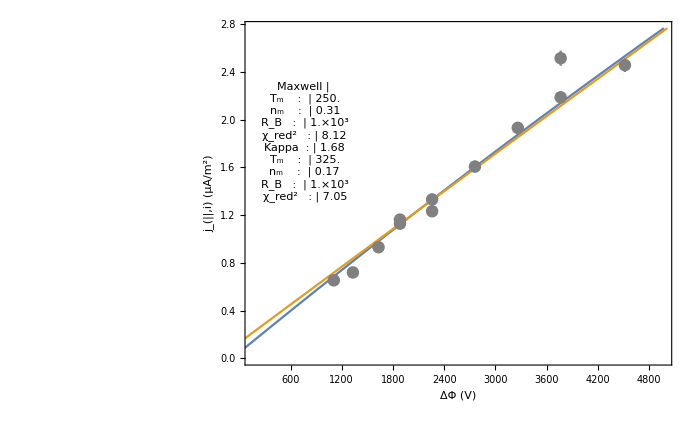

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),*)
```

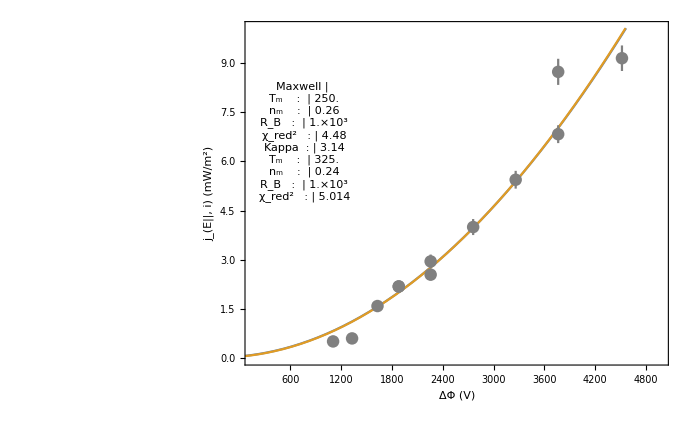

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

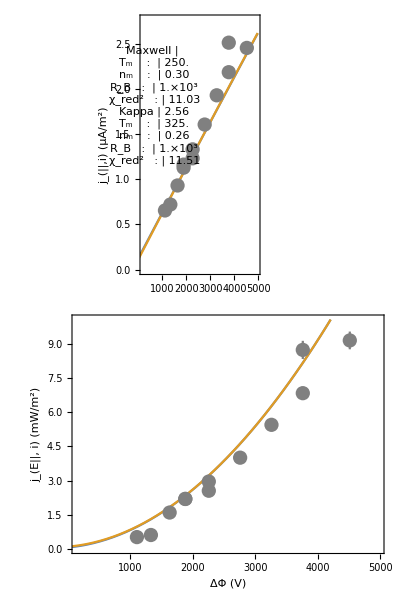

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

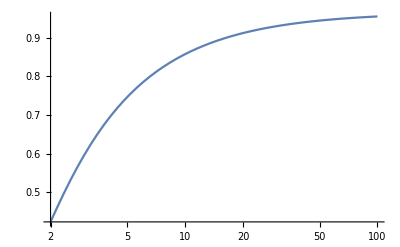

```mathematica
LogLinearPlot[LKMwellDensFac[100/50,RB],{RB,2,100},PlotRange->Full]
```

#### Save plots

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];
Print[JVFilename<>" ..."];
Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180329/ ...

Orb1694__JVFit__inds_100-126__Automatic-fixT.png ...

Orb1694__JeVFit__inds_100-126__Automatic-fixT.png ...

Orb1694__combJVJeVFit__inds_100-126__Automatic-fixT.png ...

Done!